# Juego de la vida

## B3S23

Antes en notebooks/B3S23.nb

```mathematica
NotebookDirectory[]
```

/home/rediax/Documents/ESCOM/TT_A114/Simulator/training/

## Functions

```mathematica
ContarPatrones[matrices_List,patrones_List]:=Module[
{subBloques},
subBloques=Partition[#,{3,3},{1,1}]&/@matrices;
AssociationMap[
Function[
p,
Module[
{centro=p[[1]],sumaExt=p[[2]]},
Count[Flatten[#,1],b_/;b[[2,2]]===centro&&(Total[b,2]-b[[2,2]])===sumaExt]&/@subBloques]
],
patrones]
]
```

```mathematica
lifeCentroids=Flatten[Table[{6+5i,3+5j},{i,0,2},{j,0,5}],1];
findRule[path_String]:=Module[
{f,fOrig},
f=Import[path][[1]];
fOrig=f;
Do[
f[[1,lifeCentroids[[i,1]],lifeCentroids[[i,2]]]]=f[[2,lifeCentroids[[i,1]],lifeCentroids[[i,2]]]]+2;
,
{i,1,Length[lifeCentroids]}
];
GraphicsRow[{
ArrayPlot[fOrig[[1,4;;18]],ColorRules->{0->White,1->Black,2->White,3->Black}],
ArrayPlot[f[[1,4;;18]],ColorRules->{0->White,1->Black,2->Orange,3->Blue}]
}]
]
```

```mathematica
countOnes[evo_List]:=Module[{},
Total@Transpose@Flatten[evo,{{1},{2,3}}]
]
```

```mathematica
metricsEvo[evo_List]:=Module[
{series,T,born,death,live},series=Transpose[Flatten[evo,{{1},{2,3}}]];(*cada fila=serie temporal de una celda*)T=Length[series[[1]]];(*número de generaciones*)born=ConstantArray[0,T-1];
death=ConstantArray[0,T-1];
live=ConstantArray[0,T-1];
Do[Do[Which[s[[t]]==0&&s[[t+1]]==1,born[[t]]++,s[[t]]==1&&s[[t+1]]==0,death[[t]]++,s[[t]]==1&&s[[t+1]]==1,live[[t]]++],{t,1,T-1}],{s,series}];
<|"born"->born,"death"->death,"live"->live|>]
```

```mathematica
plotsStats[base_List,evos_List,plotLegend_List]:=Module[
{baseC,liveProportion,data,baseD,dataD,dataB,dataL,labels,sharedLegend,dblPlots},
baseC=countOnes[base];
labels=Join[{"B3/S23"},plotLegend];

liveProportion=ListLinePlot[
Join[{baseC},countOnes[#]&/@evos],
Filling->Table[i->{1},{i,2,Length[baseC]}],
FillingStyle->Directive[Opacity[0.3]],
AxesLabel->{"paso","celdas vivas"},
PlotLegends->labels,
ImageSize->600];

data=metricsEvo[#]&/@evos;
baseD=metricsEvo[base];

dataD=Join[{baseD["death"]},data[[;;,"death"]]];
dataB=Join[{baseD["born"]},data[[;;,"born"]]];
dataL=Join[{baseD["live"]},data[[;;,"live"]]];

dblPlots=MapThread[
ListLinePlot[
#1,
ScalingFunctions->"SignedLog",
Filling->Table[i->{1},{i,2,Length[#1]}],
FillingStyle->Directive[Opacity[.1]],
PlotStyle->{Thickness[0.007]},
ImageSize->600,
PlotLegends->labels,
AxesLabel->{"paso",#2}
]&,{{dataD,dataB,dataL},{"muertes","nacimientos","sobrevivientes"}}
];

Join[{liveProportion},dblPlots]
]
```

## Configuration

### Rule B3/S23

```mathematica
SetDirectory["/home/rediax/Documents/ESCOM/TT_A114/Simulator/training/Evolutions/b3_s23"];
plotLegend={"5:Linear, 2:Linear","5:Linear, 1:Sigmoid","5:ReLU, 2:Sigmoid","5:ReLU, 2:Tanh","5:Sigmoid, 1:Sigmoid"};
name="diferencias_configuracion_1";
ex="1";
```

### Rule B3/S236

```mathematica
SetDirectory["/home/rediax/Documents/ESCOM/TT_A114/Simulator/training/Evolutions/b36_s23"];
plotLegend={"64:Linear, 2:Linear","64:Linear, 1:Sigmoid","64:ReLU, 2:Sigmoid","64:ReLU, 2:Tanh","64:Sigmoid, 1:Sigmoid"};
name="diferencias_configuracion_2";
ex="2";
```

```mathematica
SetDirectory["/home/rediax/Documents/ESCOM/TT_A114/Simulator/training/Evolutions/experimento_3"];
plotLegend={"Life", "High life"};
name="diferencias_configuracion_3";
```

```mathematica
SetDirectory["/home/rediax/Documents/ESCOM/TT_A114/Simulator/training/Evolutions/experimento_4"];
plotLegend=ToString[#]&/@Range[10];
```

## Execute

```mathematica
base=Import["./base.mat"][[1]];
linear=Import["./linear.mat"][[1]];
linearSigmoid=Import["./linear_sigmoid.mat"][[1]];
reluSigmoid=Import["./relu_sigmoid.mat"][[1]];
reluTanh=Import["./relu_tanh.mat"][[1]];
sigmoid=Import["./sigmoid.mat"][[1]];
evos={linear,linearSigmoid,reluSigmoid,reluTanh,sigmoid};
plots=plotsStats[base,evos,plotLegend];
MapThread[Export["/home/rediax/Documents/ESCOM/TT_A114/Documentation/img/experimentacion/duplicacion/gol/ex_"<>ex<>"_"<>#1<>".png",#2]&,{{"ones","death","born","live"},plots}];
```

### EX 3

```mathematica
highlife=Import["./8416.mat"][[1,;;50]];
life=Import["./224.mat"][[1,;;50]];
```

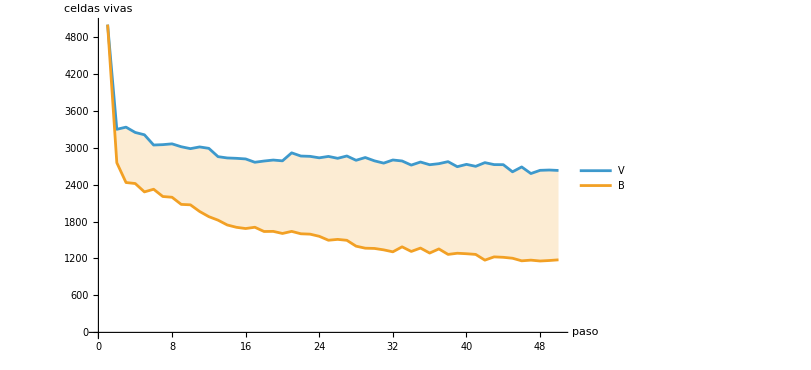

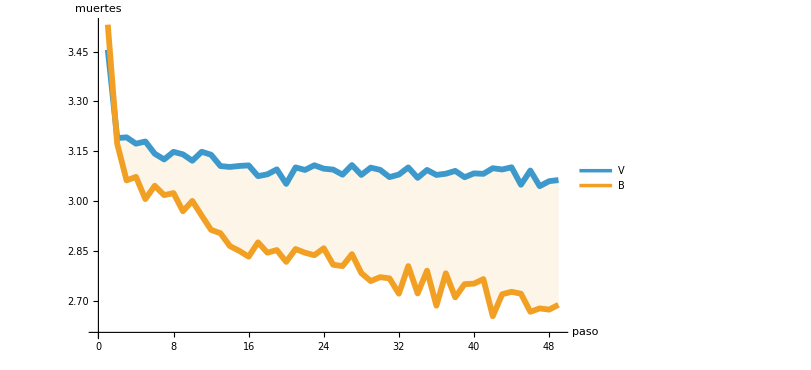
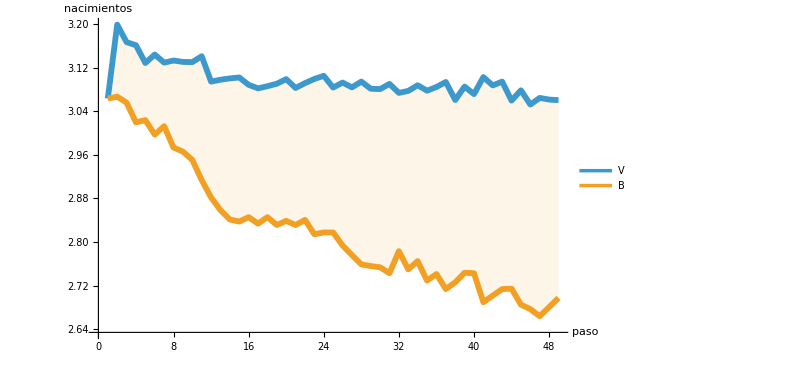
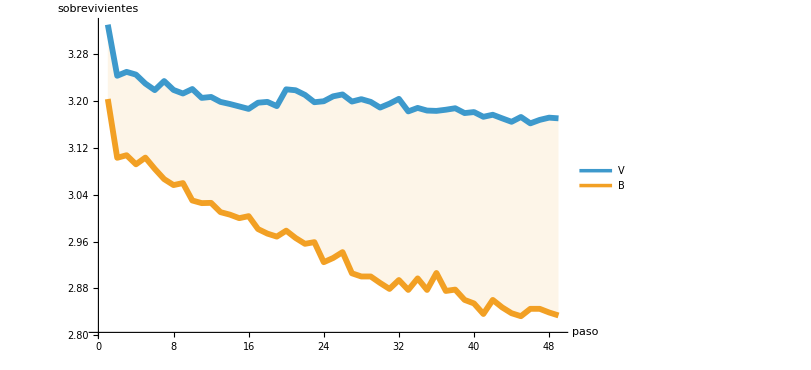

```mathematica
ListLinePlot[
countOnes[#]&/@{highlife,life},
Filling->Table[i->{1},{i,2,Length[baseC]}],
AxesLabel->{"paso","celdas vivas"},
PlotLegends->{"V","B"},
ImageSize->600]

data=metricsEvo[#]&/@{highlife,life};

dataD=data[[;;,"death"]];
dataB=data[[;;,"born"]];
dataL=data[[;;,"live"]];

dblPlots=MapThread[
ListLinePlot[
#1,
ScalingFunctions->"SignedLog",
Filling->Table[i->{1},{i,2,Length[#1]}],
FillingStyle->Directive[Opacity[.1]],
PlotStyle->{Thickness[0.007]},
ImageSize->600,
PlotLegends->{"V","B"},
AxesLabel->{"paso",#2}
]&,{{dataD,dataB,dataL},{"muertes","nacimientos","sobrevivientes"}}
]
```

## Other analysis

```mathematica
highlife=Import["./8416.mat"][[1,;;100]];
```

Import::nffil: File ./8416.mat not found during Import.

Part::partd: Part specification $Failed⟦1,1;;100⟧ is longer than depth of object.

```mathematica
contarSeguro[matriz_]:=Module[
{vecinos},
vecinos=ListConvolve[{{1,1,1},{1,0,1},{1,1,1}},matriz,{2,2},0];
Flatten[MapThread[List,{matriz,vecinos},2],1]
]
```

```mathematica
conteosPorPaso=Counts[contarSeguro[#]]&/@highlife;
serieTemporal[par_]:=Lookup[#,Key[par],0]&/@conteosPorPaso

serie03=serieTemporal[{0,3}]; 
serie06=serieTemporal[{0,6}]; 
serie12=serieTemporal[{1,2}]; 
serie13=serieTemporal[{1,3}];
```

ListConvolve::kldims: The kernel {{1,1,1},{1,0,1},{1,1,1}} and list $Failed are not both nonempty lists with the same tensor rank.

MapThread::mptd: Object $Failed at position {2, 1} in MapThread[List,{$Failed,ListConvolve[{{1,1,1},{1,0,1},{1,1,1}},$Failed,{2,2},0]},2] has only 0 of required 2 dimensions.

Counts::invrp: The argument MapThread[List,{$Failed,ListConvolve[{{1,1,1},{1,0,1},{1,1,1}},$Failed,{2,2},0]},2] is not a valid Association or a list.

ListConvolve::kldims: The kernel {{1,1,1},{1,0,1},{1,1,1}} and list 1 are not both nonempty lists with the same tensor rank.

MapThread::mptd: Object 1 at position {2, 1} in MapThread[List,{1,ListConvolve[{{1,1,1},{1,0,1},{1,1,1}},1,{2,2},0]},2] has only 0 of required 2 dimensions.

Counts::invrp: The argument MapThread[List,{1,ListConvolve[{{1,1,1},{1,0,1},{1,1,1}},1,{2,2},0]},2] is not a valid Association or a list.

ListConvolve::kldims: The kernel {{1,1,1},{1,0,1},{1,1,1}} and list 1;;100 are not both nonempty lists with the same tensor rank.

General::stop: Further output of ListConvolve::kldims will be suppressed during this calculation.

MapThread::mptd: Object 1;;100 at position {2, 1} in MapThread[List,{1;;100,ListConvolve[{{1,1,1},{1,0,1},{1,1,1}},1;;100,{2,2},0]},2] has only 0 of required 2 dimensions.

General::stop: Further output of MapThread::mptd will be suppressed during this calculation.

Counts::invrp: The argument MapThread[List,{1;;100,ListConvolve[{{1,1,1},{1,0,1},{1,1,1}},1;;100,{2,2},0]},2] is not a valid Association or a list.

General::stop: Further output of Counts::invrp will be suppressed during this calculation.

Part::pkspec1: The expression Counts[MapThread[List,{1,ListConvolve[{{1,1,1},{1,0,1},{1,1,1}},1,{2,2},0]},2]] cannot be used as a part specification.

Lookup::invrl: The argument Counts[MapThread[List,{$Failed,ListConvolve[{{1,1,1},{1,0,1},{1,1,1}},$Failed,{2,2},0]},2]] is not a valid Association or a list of rules.

Lookup::invrl: The argument Counts[MapThread[List,{1,ListConvolve[{{1,1,1},{1,0,1},{1,1,1}},1,{2,2},0]},2]] is not a valid Association or a list of rules.

Lookup::invrl: The argument Counts[MapThread[List,{1;;100,ListConvolve[{{1,1,1},{1,0,1},{1,1,1}},1;;100,{2,2},0]},2]] is not a valid Association or a list of rules.

General::stop: Further output of Lookup::invrl will be suppressed during this calculation.

Part::pkspec1: The expression Lookup[Counts[MapThread[List,{1,ListConvolve[{{1,1,1},{1,0,1},{1,1,1}},1,{2,2},0]},2]],Key[{0,3}],0] cannot be used as a part specification.

Lookup::invrl: The argument Counts[MapThread[List,{$Failed,ListConvolve[{{1,1,1},{1,0,1},{1,1,1}},$Failed,{2,2},0]},2]] is not a valid Association or a list of rules.

Lookup::invrl: The argument Counts[MapThread[List,{1,ListConvolve[{{1,1,1},{1,0,1},{1,1,1}},1,{2,2},0]},2]] is not a valid Association or a list of rules.

Lookup::invrl: The argument Counts[MapThread[List,{1;;100,ListConvolve[{{1,1,1},{1,0,1},{1,1,1}},1;;100,{2,2},0]},2]] is not a valid Association or a list of rules.

General::stop: Further output of Lookup::invrl will be suppressed during this calculation.

Part::pkspec1: The expression Lookup[Counts[MapThread[List,{1,ListConvolve[{{1,1,1},{1,0,1},{1,1,1}},1,{2,2},0]},2]],Key[{0,6}],0] cannot be used as a part specification.

Lookup::invrl: The argument Counts[MapThread[List,{$Failed,ListConvolve[{{1,1,1},{1,0,1},{1,1,1}},$Failed,{2,2},0]},2]] is not a valid Association or a list of rules.

Lookup::invrl: The argument Counts[MapThread[List,{1,ListConvolve[{{1,1,1},{1,0,1},{1,1,1}},1,{2,2},0]},2]] is not a valid Association or a list of rules.

Lookup::invrl: The argument Counts[MapThread[List,{1;;100,ListConvolve[{{1,1,1},{1,0,1},{1,1,1}},1;;100,{2,2},0]},2]] is not a valid Association or a list of rules.

General::stop: Further output of Lookup::invrl will be suppressed during this calculation.

Part::pkspec1: The expression Lookup[Counts[MapThread[List,{1,ListConvolve[{{1,1,1},{1,0,1},{1,1,1}},1,{2,2},0]},2]],Key[{1,2}],0] cannot be used as a part specification.

Lookup::invrl: The argument Counts[MapThread[List,{$Failed,ListConvolve[{{1,1,1},{1,0,1},{1,1,1}},$Failed,{2,2},0]},2]] is not a valid Association or a list of rules.

Lookup::invrl: The argument Counts[MapThread[List,{1,ListConvolve[{{1,1,1},{1,0,1},{1,1,1}},1,{2,2},0]},2]] is not a valid Association or a list of rules.

Lookup::invrl: The argument Counts[MapThread[List,{1;;100,ListConvolve[{{1,1,1},{1,0,1},{1,1,1}},1;;100,{2,2},0]},2]] is not a valid Association or a list of rules.

General::stop: Further output of Lookup::invrl will be suppressed during this calculation.

Part::pkspec1: The expression Lookup[Counts[MapThread[List,{1,ListConvolve[{{1,1,1},{1,0,1},{1,1,1}},1,{2,2},0]},2]],Key[{1,3}],0] cannot be used as a part specification.

```mathematica
paresInteres={{0,3},{0,6},{1,2},{1,3}};
total=Total[#]&/@{serie03,serie06,serie12,serie13}
N[Mean[#]]&/@{serie03,serie06,serie12,serie13}
N[#/1000000]&/@total
ListLinePlot[{serie03,serie06,serie12,serie13}]
```

{Total[Lookup[Counts[MapThread[List,{$Failed,ListConvolve[{{1,1,1},{1,0,1},{1,1,1}},$Failed,{2,2},0]},2]],Key[{0,3}],0]⟦Lookup[Counts[MapThread[List,{1,ListConvolve[{{1,1,1},{1,0,1},{1,1,1}},1,{2,2},0]},2]],Key[{0,3}],0],Lookup[Counts[MapThread[List,{1;;100,ListConvolve[{{1,1,1},{1,0,1},{1,1,1}},1;;100,{2,2},0]},2]],Key[{0,3}],0]⟧],Total[Lookup[Counts[MapThread[List,{$Failed,ListConvolve[{{1,1,1},{1,0,1},{1,1,1}},$Failed,{2,2},0]},2]],Key[{0,6}],0]⟦Lookup[Counts[MapThread[List,{1,ListConvolve[{{1,1,1},{1,0,1},{1,1,1}},1,{2,2},0]},2]],Key[{0,6}],0],Lookup[Counts[MapThread[List,{1;;100,ListConvolve[{{1,1,1},{1,0,1},{1,1,1}},1;;100,{2,2},0]},2]],Key[{0,6}],0]⟧],Total[Lookup[Counts[MapThread[List,{$Failed,ListConvolve[{{1,1,1},{1,0,1},{1,1,1}},$Failed,{2,2},0]},2]],Key[{1,2}],0]⟦Lookup[Counts[MapThread[List,{1,ListConvolve[{{1,1,1},{1,0,1},{1,1,1}},1,{2,2},0]},2]],Key[{1,2}],0],Lookup[Counts[MapThread[List,{1;;100,ListConvolve[{{1,1,1},{1,0,1},{1,1,1}},1;;100,{2,2},0]},2]],Key[{1,2}],0]⟧],Total[Lookup[Counts[MapThread[List,{$Failed,ListConvolve[{{1,1,1},{1,0,1},{1,1,1}},$Failed,{2,2},0]},2]],Key[{1,3}],0]⟦Lookup[Counts[MapThread[List,{1,ListConvolve[{{1,1,1},{1,0,1},{1,1,1}},1,{2,2},0]},2]],Key[{1,3}],0],Lookup[Counts[MapThread[List,{1;;100,ListConvolve[{{1,1,1},{1,0,1},{1,1,1}},1;;100,{2,2},0]},2]],Key[{1,3}],0]⟧]}

ListConvolve::kldims: The kernel {{1.,1.,1.},{1.,0.,1.},{1.,1.,1.}} and list $Failed are not both nonempty lists with the same tensor rank.

MapThread::intnm: Non-negative machine-sized integer expected at position 3 in MapThread[List,{$Failed,ListConvolve[{{1.,1.,1.},{1.,0.,1.},{1.,1.,1.}},$Failed,{2.,2.},0.]},2.].

Counts::invrp: The argument MapThread[List,{$Failed,ListConvolve[{{1.,1.,1.},{1.,0.,1.},{1.,1.,1.}},$Failed,{2.,2.},0.]},2.] is not a valid Association or a list.

Lookup::invrl: The argument Counts[MapThread[List,{$Failed,ListConvolve[{{1.,1.,1.},{1.,0.,1.},{1.,1.,1.}},$Failed,{2.,2.},0.]},2.]] is not a valid Association or a list of rules.

Part::pkspec1: The expression Lookup[Counts[MapThread[List,{1,ListConvolve[{{1,1,1},{1,0,1},{1,1,1}},1,{2,2},0]},2]],Key[{0,3}],0] cannot be used as a part specification.

ListConvolve::kldims: The kernel {{1.,1.,1.},{1.,0.,1.},{1.,1.,1.}} and list $Failed are not both nonempty lists with the same tensor rank.

MapThread::intnm: Non-negative machine-sized integer expected at position 3 in MapThread[List,{$Failed,ListConvolve[{{1.,1.,1.},{1.,0.,1.},{1.,1.,1.}},$Failed,{2.,2.},0.]},2.].

Counts::invrp: The argument MapThread[List,{$Failed,ListConvolve[{{1.,1.,1.},{1.,0.,1.},{1.,1.,1.}},$Failed,{2.,2.},0.]},2.] is not a valid Association or a list.

Lookup::invrl: The argument Counts[MapThread[List,{$Failed,ListConvolve[{{1.,1.,1.},{1.,0.,1.},{1.,1.,1.}},$Failed,{2.,2.},0.]},2.]] is not a valid Association or a list of rules.

Part::pkspec1: The expression Lookup[Counts[MapThread[List,{1,ListConvolve[{{1,1,1},{1,0,1},{1,1,1}},1,{2,2},0]},2]],Key[{0,6}],0] cannot be used as a part specification.

ListConvolve::kldims: The kernel {{1.,1.,1.},{1.,0.,1.},{1.,1.,1.}} and list $Failed are not both nonempty lists with the same tensor rank.

General::stop: Further output of ListConvolve::kldims will be suppressed during this calculation.

MapThread::intnm: Non-negative machine-sized integer expected at position 3 in MapThread[List,{$Failed,ListConvolve[{{1.,1.,1.},{1.,0.,1.},{1.,1.,1.}},$Failed,{2.,2.},0.]},2.].

General::stop: Further output of MapThread::intnm will be suppressed during this calculation.

Counts::invrp: The argument MapThread[List,{$Failed,ListConvolve[{{1.,1.,1.},{1.,0.,1.},{1.,1.,1.}},$Failed,{2.,2.},0.]},2.] is not a valid Association or a list.

General::stop: Further output of Counts::invrp will be suppressed during this calculation.

Lookup::invrl: The argument Counts[MapThread[List,{$Failed,ListConvolve[{{1.,1.,1.},{1.,0.,1.},{1.,1.,1.}},$Failed,{2.,2.},0.]},2.]] is not a valid Association or a list of rules.

General::stop: Further output of Lookup::invrl will be suppressed during this calculation.

Part::pkspec1: The expression Lookup[Counts[MapThread[List,{1,ListConvolve[{{1,1,1},{1,0,1},{1,1,1}},1,{2,2},0]},2]],Key[{1,2}],0] cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

{Mean[Lookup[Counts[MapThread[List,{$Failed,ListConvolve[{{1.,1.,1.},{1.,0.,1.},{1.,1.,1.}},$Failed,{2.,2.},0.]},2.]],Key[{0.,3.}],0.]⟦Lookup[Counts[MapThread[List,{1,ListConvolve[{{1,1,1},{1,0,1},{1,1,1}},1,{2,2},0]},2]],Key[{0,3}],0],Lookup[Counts[MapThread[List,{1;;100,ListConvolve[{{1,1,1},{1,0,1},{1,1,1}},1;;100,{2,2},0]},2]],Key[{0,3}],0]⟧],Mean[Lookup[Counts[MapThread[List,{$Failed,ListConvolve[{{1.,1.,1.},{1.,0.,1.},{1.,1.,1.}},$Failed,{2.,2.},0.]},2.]],Key[{0.,6.}],0.]⟦Lookup[Counts[MapThread[List,{1,ListConvolve[{{1,1,1},{1,0,1},{1,1,1}},1,{2,2},0]},2]],Key[{0,6}],0],Lookup[Counts[MapThread[List,{1;;100,ListConvolve[{{1,1,1},{1,0,1},{1,1,1}},1;;100,{2,2},0]},2]],Key[{0,6}],0]⟧],Mean[Lookup[Counts[MapThread[List,{$Failed,ListConvolve[{{1.,1.,1.},{1.,0.,1.},{1.,1.,1.}},$Failed,{2.,2.},0.]},2.]],Key[{1.,2.}],0.]⟦Lookup[Counts[MapThread[List,{1,ListConvolve[{{1,1,1},{1,0,1},{1,1,1}},1,{2,2},0]},2]],Key[{1,2}],0],Lookup[Counts[MapThread[List,{1;;100,ListConvolve[{{1,1,1},{1,0,1},{1,1,1}},1;;100,{2,2},0]},2]],Key[{1,2}],0]⟧],Mean[Lookup[Counts[MapThread[List,{$Failed,ListConvolve[{{1.,1.,1.},{1.,0.,1.},{1.,1.,1.}},$Failed,{2.,2.},0.]},2.]],Key[{1.,3.}],0.]⟦Lookup[Counts[MapThread[List,{1,ListConvolve[{{1,1,1},{1,0,1},{1,1,1}},1,{2,2},0]},2]],Key[{1,3}],0],Lookup[Counts[MapThread[List,{1;;100,ListConvolve[{{1,1,1},{1,0,1},{1,1,1}},1;;100,{2,2},0]},2]],Key[{1,3}],0]⟧]}

ListConvolve::kldims: The kernel {{1.,1.,1.},{1.,0.,1.},{1.,1.,1.}} and list $Failed are not both nonempty lists with the same tensor rank.

MapThread::intnm: Non-negative machine-sized integer expected at position 3 in MapThread[List,{$Failed,ListConvolve[{{1.,1.,1.},{1.,0.,1.},{1.,1.,1.}},$Failed,{2.,2.},0.]},2.].

Counts::invrp: The argument MapThread[List,{$Failed,ListConvolve[{{1.,1.,1.},{1.,0.,1.},{1.,1.,1.}},$Failed,{2.,2.},0.]},2.] is not a valid Association or a list.

Lookup::invrl: The argument Counts[MapThread[List,{$Failed,ListConvolve[{{1.,1.,1.},{1.,0.,1.},{1.,1.,1.}},$Failed,{2.,2.},0.]},2.]] is not a valid Association or a list of rules.

Part::pkspec1: The expression Lookup[Counts[MapThread[List,{1,ListConvolve[{{1,1,1},{1,0,1},{1,1,1}},1,{2,2},0]},2]],Key[{0,3}],0] cannot be used as a part specification.

ListConvolve::kldims: The kernel {{1.,1.,1.},{1.,0.,1.},{1.,1.,1.}} and list $Failed are not both nonempty lists with the same tensor rank.

MapThread::intnm: Non-negative machine-sized integer expected at position 3 in MapThread[List,{$Failed,ListConvolve[{{1.,1.,1.},{1.,0.,1.},{1.,1.,1.}},$Failed,{2.,2.},0.]},2.].

Counts::invrp: The argument MapThread[List,{$Failed,ListConvolve[{{1.,1.,1.},{1.,0.,1.},{1.,1.,1.}},$Failed,{2.,2.},0.]},2.] is not a valid Association or a list.

Lookup::invrl: The argument Counts[MapThread[List,{$Failed,ListConvolve[{{1.,1.,1.},{1.,0.,1.},{1.,1.,1.}},$Failed,{2.,2.},0.]},2.]] is not a valid Association or a list of rules.

Part::pkspec1: The expression Lookup[Counts[MapThread[List,{1,ListConvolve[{{1,1,1},{1,0,1},{1,1,1}},1,{2,2},0]},2]],Key[{0,6}],0] cannot be used as a part specification.

ListConvolve::kldims: The kernel {{1.,1.,1.},{1.,0.,1.},{1.,1.,1.}} and list $Failed are not both nonempty lists with the same tensor rank.

General::stop: Further output of ListConvolve::kldims will be suppressed during this calculation.

MapThread::intnm: Non-negative machine-sized integer expected at position 3 in MapThread[List,{$Failed,ListConvolve[{{1.,1.,1.},{1.,0.,1.},{1.,1.,1.}},$Failed,{2.,2.},0.]},2.].

General::stop: Further output of MapThread::intnm will be suppressed during this calculation.

Counts::invrp: The argument MapThread[List,{$Failed,ListConvolve[{{1.,1.,1.},{1.,0.,1.},{1.,1.,1.}},$Failed,{2.,2.},0.]},2.] is not a valid Association or a list.

General::stop: Further output of Counts::invrp will be suppressed during this calculation.

Lookup::invrl: The argument Counts[MapThread[List,{$Failed,ListConvolve[{{1.,1.,1.},{1.,0.,1.},{1.,1.,1.}},$Failed,{2.,2.},0.]},2.]] is not a valid Association or a list of rules.

General::stop: Further output of Lookup::invrl will be suppressed during this calculation.

Part::pkspec1: The expression Lookup[Counts[MapThread[List,{1,ListConvolve[{{1,1,1},{1,0,1},{1,1,1}},1,{2,2},0]},2]],Key[{1,2}],0] cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

{1.×10^-6 Total[Lookup[Counts[MapThread[List,{$Failed,ListConvolve[{{1.,1.,1.},{1.,0.,1.},{1.,1.,1.}},$Failed,{2.,2.},0.]},2.]],Key[{0.,3.}],0.]⟦Lookup[Counts[MapThread[List,{1,ListConvolve[{{1,1,1},{1,0,1},{1,1,1}},1,{2,2},0]},2]],Key[{0,3}],0],Lookup[Counts[MapThread[List,{1;;100,ListConvolve[{{1,1,1},{1,0,1},{1,1,1}},1;;100,{2,2},0]},2]],Key[{0,3}],0]⟧],1.×10^-6 Total[Lookup[Counts[MapThread[List,{$Failed,ListConvolve[{{1.,1.,1.},{1.,0.,1.},{1.,1.,1.}},$Failed,{2.,2.},0.]},2.]],Key[{0.,6.}],0.]⟦Lookup[Counts[MapThread[List,{1,ListConvolve[{{1,1,1},{1,0,1},{1,1,1}},1,{2,2},0]},2]],Key[{0,6}],0],Lookup[Counts[MapThread[List,{1;;100,ListConvolve[{{1,1,1},{1,0,1},{1,1,1}},1;;100,{2,2},0]},2]],Key[{0,6}],0]⟧],1.×10^-6 Total[Lookup[Counts[MapThread[List,{$Failed,ListConvolve[{{1.,1.,1.},{1.,0.,1.},{1.,1.,1.}},$Failed,{2.,2.},0.]},2.]],Key[{1.,2.}],0.]⟦Lookup[Counts[MapThread[List,{1,ListConvolve[{{1,1,1},{1,0,1},{1,1,1}},1,{2,2},0]},2]],Key[{1,2}],0],Lookup[Counts[MapThread[List,{1;;100,ListConvolve[{{1,1,1},{1,0,1},{1,1,1}},1;;100,{2,2},0]},2]],Key[{1,2}],0]⟧],1.×10^-6 Total[Lookup[Counts[MapThread[List,{$Failed,ListConvolve[{{1.,1.,1.},{1.,0.,1.},{1.,1.,1.}},$Failed,{2.,2.},0.]},2.]],Key[{1.,3.}],0.]⟦Lookup[Counts[MapThread[List,{1,ListConvolve[{{1,1,1},{1,0,1},{1,1,1}},1,{2,2},0]},2]],Key[{1,3}],0],Lookup[Counts[MapThread[List,{1;;100,ListConvolve[{{1,1,1},{1,0,1},{1,1,1}},1;;100,{2,2},0]},2]],Key[{1,3}],0]⟧]}

ListConvolve::kldims: The kernel {{1.,1.,1.},{1.,0,1.},{1.,1.,1.}} and list $Failed are not both nonempty lists with the same tensor rank.

MapThread::intnm: Non-negative machine-sized integer expected at position 3 in MapThread[List,{$Failed,ListConvolve[{{1.,1.,1.},{1.,0,1.},{1.,1.,1.}},$Failed,{2.,2.},0]},2.].

Counts::invrp: The argument MapThread[List,{$Failed,ListConvolve[{{1.,1.,1.},{1.,0,1.},{1.,1.,1.}},$Failed,{2.,2.},0]},2.] is not a valid Association or a list.

Lookup::invrl: The argument Counts[MapThread[List,{$Failed,ListConvolve[{{1.,1.,1.},{1.,0,1.},{1.,1.,1.}},$Failed,{2.,2.},0]},2.]] is not a valid Association or a list of rules.

Part::pkspec1: The expression Lookup[Counts[MapThread[List,{1,ListConvolve[{{1,1,1},{1,0,1},{1,1,1}},1,{2,2},0]},2]],Key[{0,3}],0] cannot be used as a part specification.

Lookup::invrl: The argument Counts[MapThread[List,{$Failed,ListConvolve[{{1.,1.,1.},{1.,0,1.},{1.,1.,1.}},$Failed,{2.,2.},0]},2.]] is not a valid Association or a list of rules.

Part::pkspec1: The expression Lookup[Counts[MapThread[List,{1,ListConvolve[{{1,1,1},{1,0,1},{1,1,1}},1,{2,2},0]},2]],Key[{0,6}],0] cannot be used as a part specification.

Lookup::invrl: The argument Counts[MapThread[List,{$Failed,ListConvolve[{{1.,1.,1.},{1.,0,1.},{1.,1.,1.}},$Failed,{2.,2.},0]},2.]] is not a valid Association or a list of rules.

General::stop: Further output of Lookup::invrl will be suppressed during this calculation.

Part::pkspec1: The expression Lookup[Counts[MapThread[List,{1,ListConvolve[{{1,1,1},{1,0,1},{1,1,1}},1,{2,2},0]},2]],Key[{1,2}],0] cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

ListConvolve::kldims: The kernel {{1.,1.,1.},{1.,0.,1.},{1.,1.,1.}} and list $Failed are not both nonempty lists with the same tensor rank.

MapThread::intnm: Non-negative machine-sized integer expected at position 3 in MapThread[List,{$Failed,ListConvolve[{{1.,1.,1.},{1.,0.,1.},{1.,1.,1.}},$Failed,{2.,2.},0.]},2.].

Counts::invrp: The argument MapThread[List,{$Failed,ListConvolve[{{1.,1.,1.},{1.,0.,1.},{1.,1.,1.}},$Failed,{2.,2.},0.]},2.] is not a valid Association or a list.

ListConvolve::kldims: The kernel {{1.,1.,1.},{1.,0.,1.},{1.,1.,1.}} and list $Failed are not both nonempty lists with the same tensor rank.

General::stop: Further output of ListConvolve::kldims will be suppressed during this calculation.

MapThread::intnm: Non-negative machine-sized integer expected at position 3 in MapThread[List,{$Failed,ListConvolve[{{1.,1.,1.},{1.,0.,1.},{1.,1.,1.}},$Failed,{2.,2.},0.]},2.].

General::stop: Further output of MapThread::intnm will be suppressed during this calculation.

Counts::invrp: The argument MapThread[List,{$Failed,ListConvolve[{{1.,1.,1.},{1.,0.,1.},{1.,1.,1.}},$Failed,{2.,2.},0.]},2.] is not a valid Association or a list.

General::stop: Further output of Counts::invrp will be suppressed during this calculation.

-Graphics-

### 4 Experiment

```mathematica
SetDirectory[NotebookDirectory[]];
base=Import["../CA/B3S23/base_50.mat"][[1]];
patternCount=ContarPatrones[base,Flatten[Table[{j,i},{i,0,8},{j,0,1}],1]];
```

```mathematica
names="C"<>ToString[#[[1]]]<>" N"<>ToString[#[[2]]]&/@Keys[patternCount];
total=Total[patternCount[[;;,1]]];
```

```mathematica
props=Values[patternCount]/total;propsSampled=Transpose[props]⟦1;;All;;4⟧;meansPct=(ToString[Slot["1"]]&)/@N[Mean/@Transpose[propsSampled] 100];legends=MapThread[#1<>": "<>#2<>"%"&,{names,meansPct}];
```

```mathematica
meansVec=N[Mean/@Transpose[propsSampled]] 100;
stdVec=N[StandardDeviation/@Transpose[propsSampled]] 100;
order=Ordering[meansVec,All,Greater];
namesSorted=names[[order]];
meansSorted=meansVec[[order]];
stdSorted=stdVec[[order]];
colors=If[StringStartsQ[#,"C0"],RGBColor[1, 0.8, 0.081],RGBColor[0.392, 1, 0.736]]&/@namesSorted;
n=Length[meansSorted];

lowerBound=MapThread[Max[#1-#2,0.001]&,{meansSorted,stdSorted}];
upperBound=meansSorted+stdSorted;

barChart=BarChart[meansSorted,ChartLabels->Placed[namesSorted,Axis,Rotate[#,90 Degree]&],ChartStyle->colors,PlotLabel->"Proporción de patrones (media ± std entre muestras)",ScalingFunctions->"Log"];

errorBars=Graphics[{Black,Thick,MapThread[Line[{{#1,Log[10,#2]},{#1,Log[10,#3]}}]&,{Range[n],lowerBound,upperBound}]}];

(*Etiquetas verticales,rotadas 90 grados,ancladas a la izquierda del punto*)
valueLabels=Graphics[{Black,MapThread[Text[ToString[NumberForm[#2,{Infinity,3}]]<>"%",{#1,Log[10,#3]+0.1},{-1,0},{0,1}  (*dirección del texto:vertical hacia arriba*)]&,{Range[n],meansSorted,upperBound}]}];

fplot=Show[barChart,errorBars,valueLabels,PlotRange->All,ImageSize->400,PlotRangeClipping->False,ImagePadding->{{20,1},{30,10}}];
Export["./../../../Documentation/img/experimentacion/duplicacion/gol/life_pattern_count.png",fplot]
```

./../../../Documentation/img/experimentacion/duplicacion/gol/life_pattern_count.png

### 5 Experiment

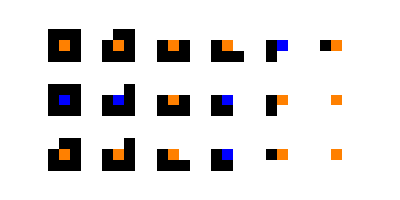

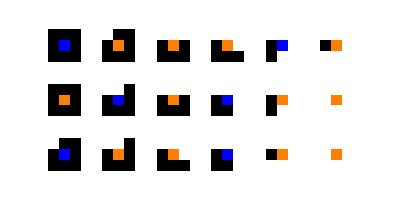

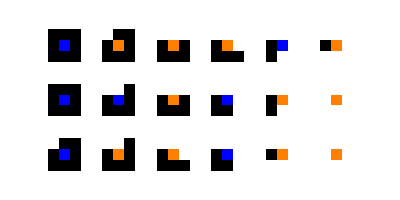

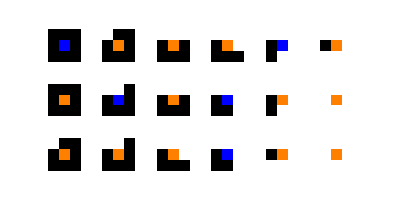

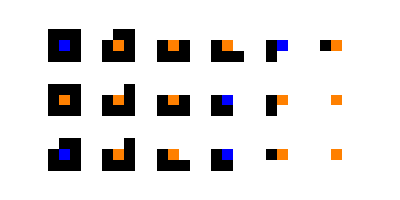

```mathematica
findRule["./life_rule_find_003.mat"]
findRule["./life_rule_find_004.mat"]
findRule["./life_rule_find_005.mat"]
findRule["./life_rule_find_01.mat"]
findRule["./life_rule_find_02.mat"]
```

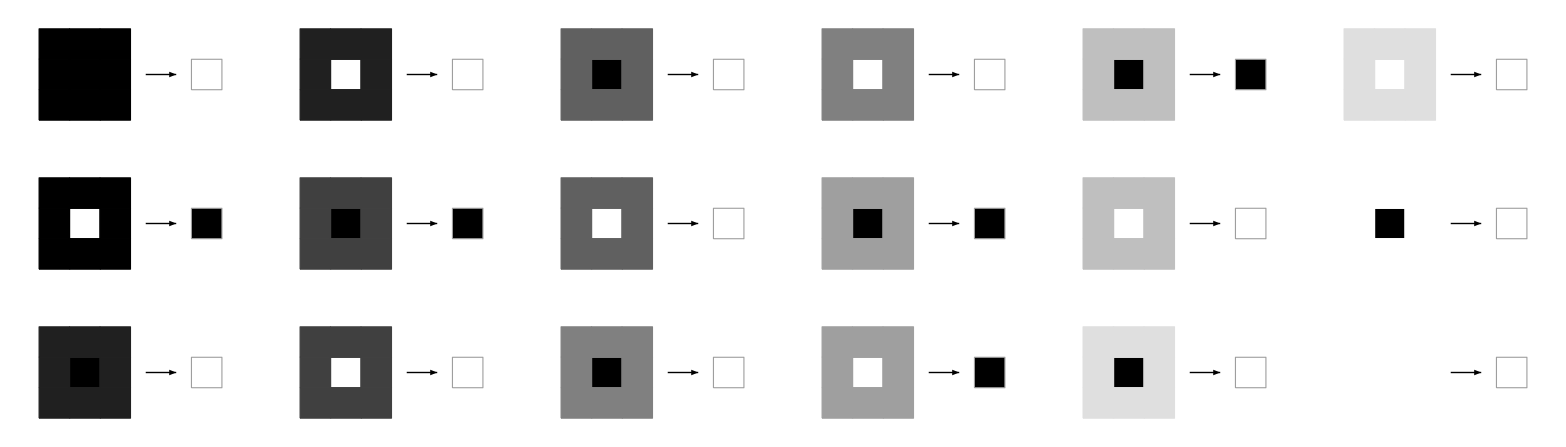

```mathematica
RulePlot[CellularAutomaton[<|"Dimension"->2,"OuterTotalisticCode"->73952|>]]
```

```mathematica
r73952=Import["./b38_s236.mat"][[1]];
nca003=Import["./003.mat"][[1]];
r73952==nca003
patternCount[{1,8}]//Mean//N
patternCount[{1,8}]//StandardDeviation//N
total/(patternCount[{1,8}]//StandardDeviation//N)
plot5=ArrayPlot[r73952[[-1,;;30,;;30]]]
plot6=ArrayPlot[nca003[[-1,;;30,;;30]]]
```

True

1.58416

1.4647

6556.97

-Graphics-

-Graphics-

```mathematica
Export["/home/rediax/Documents/ESCOM/TT_A114/Documentation/img/experimentacion/duplicacion/gol/"<>"perdida_objetivo"<>".png",plot1];
Export["/home/rediax/Documents/ESCOM/TT_A114/Documentation/img/experimentacion/duplicacion/gol/"<>"rule_b3_s23"<>".png",plot2];
Export["/home/rediax/Documents/ESCOM/TT_A114/Documentation/img/experimentacion/duplicacion/gol/"<>"rule_b3_s236"<>".png",plot3];
Export["/home/rediax/Documents/ESCOM/TT_A114/Documentation/img/experimentacion/duplicacion/gol/"<>"b3_s236_proportion"<>".png",plot4];
Export["/home/rediax/Documents/ESCOM/TT_A114/Documentation/img/experimentacion/duplicacion/gol/"<>"r73952"<>".png",plot5];
Export["/home/rediax/Documents/ESCOM/TT_A114/Documentation/img/experimentacion/duplicacion/gol/"<>"nca003"<>".png",plot6];
```

## Proporciones de estados y cambios

Compara varias evoluciones binarias que ocupan el mismo espacio y duran los mismos pasos. Se grafican dos proporciones respecto al total de celdas, con el paso en el eje x y la proporción en el eje y:

Unos en cada paso, de 0 al máximo observado.

Nacimientos (0 → 1), muertes (1 → 0) y quietos (sin cambio) en la transición del paso t − 1 al paso t, de 0 a 1. Las tres suman 1.

Cada evolución es una línea delgada y la línea gruesa es el promedio de todas.

## Archivos

Rutas relativas a la carpeta del notebook. Todas las evoluciones deben tener las mismas dimensiones.

```mathematica
SetDirectory[NotebookDirectory[]];
archivos=FileNames["*.mat","/home/rediax/Documents/ESCOM/Trabajo-Terminal/Simulator/training/NCA/B3S23_NR/1_01111111/best_evos"];
```

```mathematica
leerEvolucion[archivo_String]:=First[Import[archivo,"MAT"]];
evoluciones=leerEvolucion /@ archivos;
{Length[evoluciones],Union[Dimensions /@ evoluciones]}
```

{10,{{101,69,69}}}

## Medidas

```mathematica
celdas[evo_]:=Times @@ Rest[Dimensions[evo]];
proporciones[evo_]:=<|"Unos"->N[Total[evo,{2,3}]/celdas[evo]]|>;
cambios[evo_]:=With[{d=Differences[evo],n=N[celdas[evo]]},
	<|"Nacimientos"->Total[Clip[d,{0,1}],{2,3}]/n,
	  "Muertes"->Total[Clip[-d,{0,1}],{2,3}]/n,
	  "Quietos"->Total[1-Abs[d],{2,3}]/n|>];
datosProporciones=proporciones /@ evoluciones;
datosCambios=cambios /@ evoluciones;
```

## Gráficas

maximo es el límite superior del eje y (1 por defecto); las marcas del eje y las líneas guía usan las mismas divisiones. Con una sola medida no se agrega leyenda; el título la nombra.

```mathematica
colores=<|
	"Unos"->RGBColor["#2a78d6"],
	"Nacimientos"->RGBColor["#2a78d6"],"Muertes"->RGBColor["#eb6834"],"Quietos"->RGBColor["#1baf7a"]|>;
graficar[datos_List,pasos_List,titulo_String,maximo_ : 1]:=Module[{medidas=Keys[First[datos]],divisiones=FindDivisions[{0,maximo},6],grafica},
	grafica=Show[
		ListLinePlot[Flatten[Table[Transpose[{pasos,d[m]}],{m,medidas},{d,datos}],1],
			PlotStyle->Flatten[Table[ConstantArray[Directive[colores[m],Opacity[0.3],AbsoluteThickness[1]],Length[datos]],{m,medidas}],1]],
		ListLinePlot[Table[Transpose[{pasos,Mean[#[m] & /@ datos]}],{m,medidas}],
			PlotStyle->(Directive[colores[#],AbsoluteThickness[2]] & /@ medidas)],
		PlotRange->{{Min[pasos],Max[pasos]},{0,maximo}},Frame->True,Axes->False,
		FrameTicks->{{{#,NumberForm[N[#],{2,1}]} & /@ divisiones,None},{Automatic,None}},
		FrameLabel->{"Paso","Proporción"},PlotLabel->titulo,
		GridLines->{None,divisiones},GridLinesStyle->Directive[GrayLevel[0.85]],
		FrameStyle->GrayLevel[0.4],FrameTicksStyle->Directive[Black,11],LabelStyle->Directive[Black,12],
		ImageSize->400,AspectRatio->3/4];
	If[Length[medidas]==1,grafica,
		Legended[grafica,LineLegend[Values[KeyTake[colores,medidas]],medidas,LegendMarkerSize->{20,10}]]]];
pasos=Length[First[evoluciones]];
```

{{0.498005,0.331653,0.302247,0.287125,0.26528,0.245327,0.221382,0.21088,0.187776,0.172653,0.152279,0.130855,0.113212,0.10355,0.094938,0.0829658,0.0726738,0.063222,0.0581811,0.0520899,0.0470489,0.0415879,0.0378072,0.0340265,0.0298257,0.0281453,0.0270951,0.026255,0.0247847,0.0245747,0.0239445,0.0226843,0.0218442,0.0216341,0.0216341,0.0216341,0.0216341,0.0216341,0.0216341,0.0216341,0.0216341,0.0216341,0.0216341,0.0216341,0.0216341,0.0216341,0.0216341,0.0216341,0.0216341,0.0216341}}

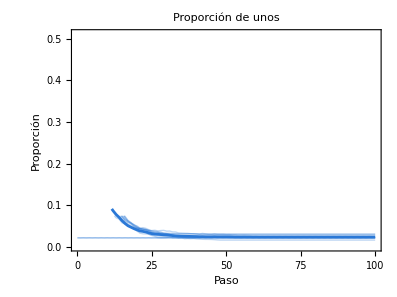

```mathematica
graficaProporciones=graficar[datosProporciones,Range[0,pasos-1],"Proporción de unos",Max[Values /@ datosProporciones]]
```

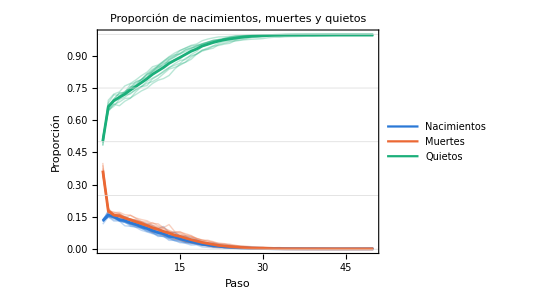

```mathematica
graficaCambios=graficar[datosCambios,Range[1,pasos-1],"Proporción de nacimientos, muertes y quietos"]
```

## Exportar

```mathematica
Export["../../../Documentation/img/experimentacion/duplicacion/gol/b3s23_reduction_1s.png",graficaProporciones,ImageResolution->200];
Export["../../../Documentation/img/experimentacion/duplicacion/gol/b3s23_reduction_changes.png",graficaCambios,ImageResolution->200];
```

Antes en notebooks/gol_proportions.nb

## B3S23 con varias evoluciones

Antes en notebooks/B3S23_multi.nb

```mathematica
ContarPatrones[matrices_List,patrones_List]:=Module[
{subBloques},
subBloques=Partition[#,{3,3},{1,1}]&/@matrices;
AssociationMap[
Function[
p,
Module[
{centro=p[[1]],sumaExt=p[[2]]},
Count[Flatten[#,1],b_/;b[[2,2]]===centro&&(Total[b,2]-b[[2,2]])===sumaExt]&/@subBloques]
],
patrones]
]
```

```mathematica
SeedRandom[42];
evos=ParallelTable[
CellularAutomaton[
{224,{2,{{2,2,2},{2,1,2},{2,2,2}}},{1,1}},
RandomInteger[{0,1},{100,100}],
100][[2;;]]
,{i,Range[100]}];
```

```mathematica
allevos=Flatten[evos,1];
```

```mathematica
patternCount=ContarPatrones[allevos,Flatten[Table[{j,i},{i,0,8},{j,0,1}],1]];
```

```mathematica
Iconize[patternCount]
```

```mathematica
patternCount=;
```

```mathematica
names="C"<>ToString[#[[1]]]<>" N"<>ToString[#[[2]]]&/@Keys[patternCount];
total=Total[patternCount[[;;,1]]];
```

```mathematica
props=Values[patternCount]/total;propsSampled=Transpose[props]⟦1;;All;;4⟧;meansPct=(ToString[Slot["1"]]&)/@N[Mean/@Transpose[propsSampled] 100];legends=MapThread[#1<>": "<>#2<>"%"&,{names,meansPct}];
```

```mathematica
meansVec=N[Mean/@Transpose[propsSampled]] 100;
stdVec=N[StandardDeviation/@Transpose[propsSampled]] 100;
order=Ordering[meansVec,All,Greater];
namesSorted=names[[order]];
meansSorted=meansVec[[order]];
stdSorted=stdVec[[order]];
colors=If[StringStartsQ[#,"C0"],RGBColor[1, 0.8, 0.081],RGBColor[0.392, 1, 0.736]]&/@namesSorted;
n=Length[meansSorted];

lowerBound=MapThread[Max[#1-#2,0.001]&,{meansSorted,stdSorted}];
upperBound=meansSorted+stdSorted;

barChart=BarChart[meansSorted,ChartLabels->Placed[namesSorted,Axis,Rotate[#,90 Degree]&],ChartStyle->colors,PlotLabel->"Proporción de patrones (media ± std entre muestras)",ScalingFunctions->"Log"];

errorBars=Graphics[{Black,Thick,MapThread[Line[{{#1,Log[10,#2]},{#1,Log[10,#3]}}]&,{Range[n],lowerBound,upperBound}]}];

(*Etiquetas verticales,rotadas 90 grados,ancladas a la izquierda del punto*)
valueLabels=Graphics[{Black,MapThread[Text[ToString[NumberForm[#2,{Infinity,3}]]<>"%",{#1,Log[10,#3]+0.1},{-1,0},{0,1}  (*dirección del texto:vertical hacia arriba*)]&,{Range[n],meansSorted,upperBound}]}];

fplot=Show[barChart,errorBars,valueLabels,PlotRange->All,ImageSize->400,PlotRangeClipping->False,ImagePadding->{{20,1},{30,10}}];
```

```mathematica
SetDirectory[NotebookDirectory[]];
Export["./../../../Documentation/img/experimentacion/duplicacion/gol/life_pattern_count.png",fplot]
```

./../../../Documentation/img/experimentacion/duplicacion/gol/life_pattern_count.png

```mathematica
count=Counts[Flatten[#]]&/@allevos;
```

```mathematica
count[[;;3]]
```

{<|0→7214,1→2786|>,<|1→2613,0→7387|>,<|0→7468,1→2532|>}

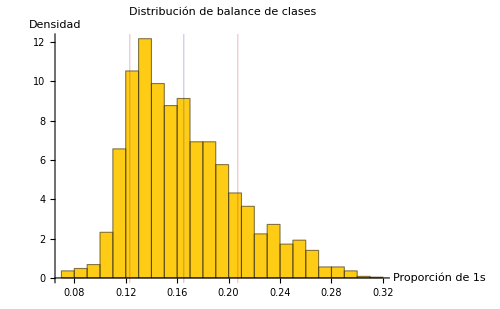

```mathematica
prop1=(#[1]/(#[0]+#[1]))&/@datos;
media=N[Mean[prop1]];
std=N[StandardDeviation[prop1]];

fplot=Histogram[prop1,Automatic,"PDF",ColorFunction->Function[{y}, RGBColor[1, 0.8, 0.081]],
GridLines->{{
{media,Directive[RGBColor[0, 0.107, 0.707],Thick]},
{media-std,Directive[RGBColor[0.707, 0, 0.128],Thick]},
{media+std,Directive[RGBColor[0.707, 0, 0.128],Thick]}},None},
AxesLabel->{"Proporción de 1s","Densidad"},PlotLabel->"Distribución de balance de clases",
PlotLegends->{"Media"<>ToString[NumberForm[media,{Infinity,3}]],"Verde = media ± std"},
ImageSize->500]
```

```mathematica
prop1=(#[1]/(#[0]+#[1]))&/@datos;
media=N[Mean[prop1]];
std=N[StandardDeviation[prop1]];

colorMedia=RGBColor[0,0.107,0.707];
colorStd=RGBColor[0.707,0,0.128];

fplot=Histogram[prop1,Automatic,"PDF",ColorFunction->Function[{y},RGBColor[1,0.8,0.081]],GridLines->{{{media,Directive[colorMedia,Thick]},{media-std,Directive[colorStd,Thick]},{media+std,Directive[colorStd,Thick]}},None},AxesLabel->{"Proporción de 1s","Densidad"},PlotLabel->"Distribución de balance de clases",ImageSize->500];

legend=LineLegend[{Directive[colorMedia,Thick],Directive[colorStd,Thick]},{"Media = "<>ToString[NumberForm[media,{Infinity,3}]],"Media ± std = "<>ToString[NumberForm[media-std,{Infinity,3}]]<>" / "<>ToString[NumberForm[media+std,{Infinity,3}]]}];

fplot=Legended[fplot,Placed[legend,{0.99,0.55}]];
```

```mathematica
SetDirectory[NotebookDirectory[]];
Export["./../../../Documentation/img/experimentacion/duplicacion/gol/life_state_distribution.png",fplot]
```

./../../../Documentation/img/experimentacion/duplicacion/gol/life_state_distribution.png

```mathematica
100*100
```

10000

```mathematica
d2=Count[Flatten[#],1]&/@#&/@evos;
```

```mathematica
means=Mean[d2];
```

```mathematica
fplot=ListLinePlot[d2n,ColorFunction->Function[{x,y},RGBColor[1,1-Clip[Abs[y-means[[Round[x]]]]/maxDesv,{0,1}],1-Clip[Abs[y-means[[Round[x]]]]/maxDesv,{0,1}]]],ColorFunctionScaling->False,(*---Ejes y título---*)AxesLabel->{"Paso","Proporción de 1s"},PlotLabel->"Evolución de proporción de 1s por muestra",(*---Formato general---*)PlotRange->All,ImageSize->Medium];
```

```mathematica
SetDirectory[NotebookDirectory[]];
Export["./../../../Documentation/img/experimentacion/duplicacion/gol/life_all_steps.png",fplot];
```

## Similitud entre vectores de regla

Cada evolución parte de la configuración de 69 × 69 que contiene los 512 patrones de 3 × 3 en el orden de Tuples[{0,1},{3,3}] (23 × 23 bloques; los últimos 17 están en cero). Después de un paso, el centro de cada bloque es la salida de la regla para ese patrón, por lo que los centros del último paso forman el vector de regla. Se comparan los vectores de dos evoluciones con la distancia de Manhattan.

## Archivos

Rutas relativas a la carpeta del notebook. archivoA es la referencia.

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
archivoA="../CA/B3S23/base.mat";
archivoB="../NCA/B3S23_NR/1_01111111/16-16-tanh_1-sigmoid_evo.mat";
```

## Funciones

```mathematica
patrones=Tuples[{0,1},{3,3}];
centros=Flatten[Table[{i,j},{i,2,69,3},{j,2,69,3}],1];
leerEvolucion[archivo_String]:=First[Import[archivo,"MAT"]];
vectorRegla[evolucion_]:=Extract[Last[evolucion],centros][[;; Length[patrones]]];
```

## Verificación

Ambas evoluciones deben medir 69 × 69 y partir de la misma configuración.

```mathematica
evoA=leerEvolucion[archivoA];
evoB=leerEvolucion[archivoB];
{Dimensions[evoA],Dimensions[evoB],First[evoA]==First[evoB]}
```

{{2,69,69},{2,69,69},True}

## Distancia de Manhattan

```mathematica
vectorA=vectorRegla[evoA];
vectorB=vectorRegla[evoB];
Length[vectorA]
distancia=ManhattanDistance[vectorA,vectorB]
(distancia/Length[vectorA])*100//N
```

512

98

19.1406

Patrones que difieren y tipo de error ({A, B}: {1, 0} la regla B no activa la célula y {0, 1} la activa de más).

```mathematica
diferencias=Pick[Range[Length[vectorA]],Unitize[vectorA-vectorB],1];
Counts[Transpose[{vectorA[[diferencias]],vectorB[[diferencias]]}]]
```

<|{1,0}→35,{0,1}→63|>

## Visualización

Vectores acomodados en 16 × 32 (fila por fila, patrón 0 arriba a la izquierda).

```mathematica
GraphicsRow[{
	ArrayPlot[Partition[vectorA,32],Mesh->True,PlotLabel->"A"],
	ArrayPlot[Partition[vectorB,32],Mesh->True,PlotLabel->"B"],
	ArrayPlot[Partition[Abs[vectorA-vectorB],32],Mesh->True,ColorRules->{1->Red,0->White},PlotLabel->"Diferencias"]
	},ImageSize->900]
```

-Graphics-

Patrones con diferencia, etiquetados como número de patrón: A → B.

```mathematica
Grid[Partition[
	Labeled[ArrayPlot[patrones[[#]],Mesh->True,ImageSize->40],Row[{#-1,": ",vectorA[[#]],"→",vectorB[[#]]}]] & /@ diferencias,
	UpTo[8]]]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- |  |  |  |  |  |

Antes en notebooks/gol_similarity.nb

## Prueba de B3S23

Antes en NCA/B3S23/test.nb

```mathematica
tuples=Tuples[{0,1},{3,3}];
```

```mathematica
tuples=Tuples[{0,1},{3,3}];

n=Length[tuples];
side=Ceiling[Sqrt[n]];

(*Rellena la lista de matrices con ceros hasta side^2,manteniendo cada bloque 3x3*)
padded=PadRight[tuples,{side^2,3,3}];

(*Acomoda los bloques en una cuadrícula side x side*)
blocks=Partition[padded,side];

(*Aplana los bloques en una sola matriz grande*)
bigMatrix=ArrayFlatten[blocks];
```

```mathematica
ArrayPlot[bigMatrix,Mesh->{Range[0,27*3,3],Range[0,27*3,3]},MeshStyle->Directive[Gray,Thick]]
```

-Graphics-

```mathematica
27*3
```

81

```mathematica
SetDirectory[(NotebookDirectory[]<>"../NCA/B3S23/")];
```

```mathematica
Export["test.mat",{bigMatrix}]
```

test.mat

```mathematica
Dimensions[bigMatrix]
```

{69,69}

```mathematica
fns=FileNames["0*.mat","./"];
data=Import[#,"MAT"]&/@fns;
```

```mathematica
base=Import["../../CA/B3S23/base.mat","MAT"];
```

```mathematica
datos=AssociationMap[Import[#,"MAT"]&,fns];
```

```mathematica
centers=Flatten[Table[{i,j},{i,Range[2,69,3]},{j,Range[2,69,3]}],1];
```

```mathematica
base[[1,2]]==#&/@datos[[;;,1,2]]
```

<|./t_00001.mat→True,./t_00002.mat→True,./t_00003.mat→True,./t_00004.mat→True,./t_00005.mat→True,./t_00006.mat→True,./t_00007.mat→True,./t_00008.mat→True,./t_00009.mat→True,./t_0001.mat→True,./t_0002.mat→True,./t_0003.mat→True,./t_0004.mat→True,./t_0005.mat→True,./t_0006.mat→True,./t_0007.mat→True,./t_0008.mat→True,./t_0009.mat→True,./t_001.mat→True,./t_002.mat→True,./t_003.mat→True,./t_004.mat→True,./t_005.mat→True,./t_006.mat→True,./t_007.mat→True,./t_008.mat→True,./t_009.mat→True,./t_01.mat→True,./t_02.mat→False,./t_03.mat→False|>

```mathematica
basevector=Flatten[Part[base[[1,2]],#[[1]],#[[2]]]&/@{#}&/@centers];
```

```mathematica
vectors=Table[
Flatten[Part[i,#[[1]],#[[2]]]&/@{#}&/@centers],
{i,datos[[;;,1,2]]}
];
```

```mathematica
names=ToExpression["0."<>StringJoin[Characters[#][[4;;-5]]]]&/@Keys[datos];
```

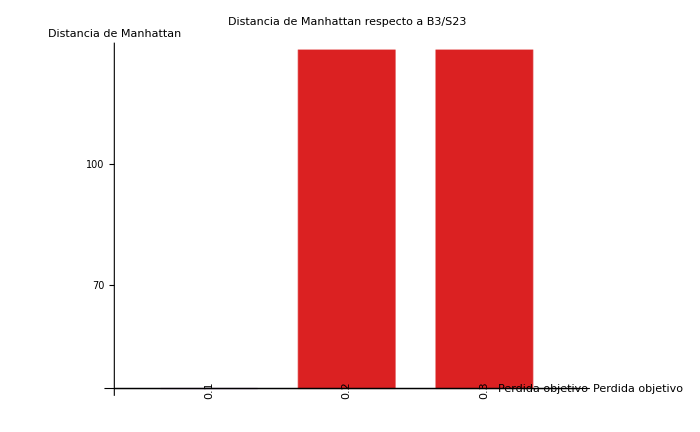

```mathematica
distancias=ManhattanDistance[basevector,#]&/@vectors;
orden=Reverse@Ordering[distancias,All,Greater];
namesSorted=names[[orden]];
distSorted=distancias[[orden]];

primerNoCero=FirstPosition[distSorted,x_/;x>0][[1]];
mask=Table[distSorted[[i]]>0||i==primerNoCero-1,{i,Length[distSorted]}];

namesFiltered=Pick[namesSorted,mask];
distFiltered=Pick[distSorted,mask];

(*Colorear según el VALOR,no según la posición*)
colorFunc=ColorData["Rainbow"];
valoresEscalados=Rescale[distFiltered]; (*normaliza entre 0 y 1*)
coloresPorValor=colorFunc/@valoresEscalados;

fplot=BarChart[distFiltered,ChartStyle->coloresPorValor,ChartLabels->Placed[Rotate[#,90 Degree]&/@namesFiltered,Axis],ScalingFunctions->"Log",AxesLabel->{"Perdida objetivo","Distancia de Manhattan"},PlotLabel->"Distancia de Manhattan respecto a B3/S23",ImageSize->700,LabelStyle->Directive[FontSize->11],BarSpacing->0.42]
```

```mathematica
SetDirectory[(NotebookDirectory[]<>"../NCA/B3S23/")];
Export["./../../../../Documentation/img/experimentacion/duplicacion/gol/b3s23_loss.png",fplot]
```

./../../../../Documentation/img/experimentacion/duplicacion/gol/b3s23_loss.png

## Datos de B3S23

Antes en NCA/B3S23/data.nb

```mathematica
SetDirectory[(NotebookDirectory[]<>"../NCA/B3S23/")];
```

```mathematica
data=Table[Import["b3_s23_2_"<>ToString[IntegerString[i,10,2]]<>".csv","Data"],{i,Range[1,10]}];
```

```mathematica
data=Table[Import["b3_s23_3_"<>ToString[IntegerString[i,10,2]]<>".csv","Data"],{i,{5,6,8,9,10}}];
```

```mathematica
data[[;;,-1]]//TableForm
```

25 | 0.160522
25 | 0.126947
25 | 0.297684
25 | 0.297686
25 | 0.374806

```mathematica
plot=ListLinePlot[#[[2;;UpTo[12]]]&/@data,PlotRange->{{0,Automatic}, All},PlotLegends->{"4:8:Sigmoid & 1:Sigmoid","4:8:ReLU      & 2:TanH","4:8:Linear    & 1:Sigmoid","4:8:Linear    & 2:Linear","4:8:ReLU     & 2:Sigmoid"}];
Export["./../../../../Documentation/img/experimentacion/duplicacion/gol/gol_funciones_2.png",plot];
```

```mathematica
Min[#[[2;;,2]]]&/@data
```

{0.160522,0.126947,0.297384,0.297383,0.374648}

```mathematica
data
```

{{{epoch,loss},{0,0.459213},{5,0.330312},{10,0.179096},{15,0.164081},{20,0.161235},{25,0.160522},{30,0.159973},{35,0.159927},{40,0.159576},{45,0.159492},{50,0.159505}},{{epoch,loss},{0,0.790261},{5,0.139739},{10,0.12723},{15,0.127013},{20,0.126965},{25,0.126947},{30,0.126939},{35,0.126935},{40,0.126932},{45,0.126931},{50,0.12693}},{{epoch,loss},{0,0.474087},{5,0.297575},{10,0.297678},{15,0.297418},{20,0.297478},{25,0.297684},{30,0.297427},{35,0.297667},{40,0.297538},{45,0.297427},{50,0.297686}},{{epoch,loss},{0,0.518469},{5,0.297565},{10,0.297673},{15,0.297419},{20,0.297483},{25,0.297686},{30,0.29743},{35,0.297673},{40,0.297541},{45,0.297434},{50,0.297692}},{{epoch,loss},{0,0.715905},{5,0.390955},{10,0.375045},{15,0.374798},{20,0.374764},{25,0.374806},{30,0.37471},{35,0.37476},{40,0.374772},{45,0.374718},{50,0.374823}}}

## Prueba de B3S23 sin reducción

Antes en NCA/B3S23_NR/test.nb

```mathematica
tuples=Tuples[{0,1},{3,3}];
n=Length[tuples];
side=Ceiling[Sqrt[n]];
padded=PadRight[tuples,{side^2,3,3}];
blocks=Partition[padded,side];
bigMatrix=ArrayFlatten[blocks];
centers=Flatten[Table[{i,j},{i,Range[2,69,3]},{j,Range[2,69,3]}],1];
ArrayPlot[bigMatrix,Mesh->{Range[0,27*3,3],Range[0,27*3,3]},MeshStyle->Directive[Gray,Thick]]
```

-Graphics-

```mathematica
SetDirectory[(NotebookDirectory[]<>"../NCA/B3S23_NR/")];
data=Import[#,"MAT"]&/@fns;
datos=AssociationMap[Import[#,"MAT"]&,fns];
```

{}

```mathematica
base=Import["../../CA/B3S236/base.mat","MAT"];
```

```mathematica
base[[1,2]]==#&/@datos[[;;,1,2]]
```

<|./t_00001.mat→True,./t_00002.mat→True,./t_00003.mat→True,./t_00004.mat→True,./t_00005.mat→True,./t_00006.mat→True,./t_00007.mat→True,./t_00008.mat→True,./t_00009.mat→True,./t_0001.mat→True,./t_0002.mat→True,./t_0003.mat→True,./t_0004.mat→True,./t_0005.mat→True,./t_0006.mat→True,./t_0007.mat→True,./t_0008.mat→True,./t_0009.mat→True,./t_001.mat→True,./t_002.mat→False,./t_003.mat→False,./t_004.mat→False,./t_005.mat→False,./t_006.mat→False,./t_007.mat→False,./t_008.mat→False,./t_009.mat→False,./t_01.mat→False,./t_02.mat→False,./t_03.mat→False|>

```mathematica
basevector=Flatten[Part[base[[1,2]],#[[1]],#[[2]]]&/@{#}&/@centers];
```

```mathematica
vectors=Table[
Flatten[Part[i,#[[1]],#[[2]]]&/@{#}&/@centers],
{i,datos[[;;,1,2]]}
];
```

```mathematica
names=ToExpression["0."<>StringJoin[Characters[#][[6;;-5]]]]&/@Keys[datos];
```

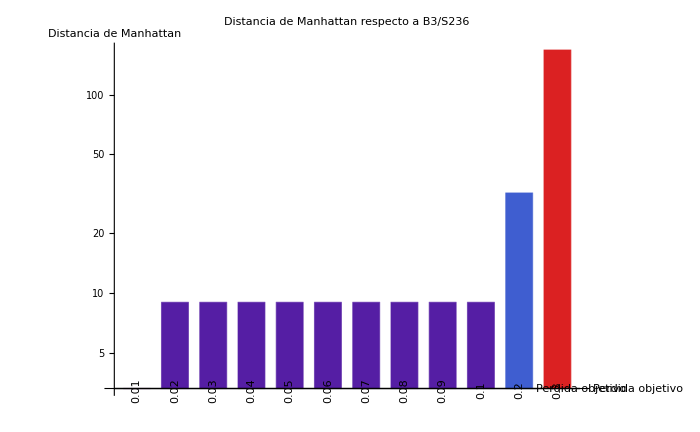

```mathematica
distancias=ManhattanDistance[basevector,#]&/@vectors;
orden=Reverse@Ordering[distancias,All,Greater];
namesSorted=names[[orden]];
distSorted=distancias[[orden]];

primerNoCero=FirstPosition[distSorted,x_/;x>0][[1]];
mask=Table[distSorted[[i]]>0||i==primerNoCero-1,{i,Length[distSorted]}];

namesFiltered=Pick[namesSorted,mask];
distFiltered=Pick[distSorted,mask];

(*Colorear según el VALOR,no según la posición*)
colorFunc=ColorData["Rainbow"];
valoresEscalados=Rescale[distFiltered]; (*normaliza entre 0 y 1*)
coloresPorValor=colorFunc/@valoresEscalados;

fplot=BarChart[distFiltered,ChartStyle->coloresPorValor,ChartLabels->Placed[Rotate[#,90 Degree]&/@namesFiltered,Axis],ScalingFunctions->"Log",AxesLabel->{"Perdida objetivo","Distancia de Manhattan"},PlotLabel->"Distancia de Manhattan respecto a B3/S236",ImageSize->700,LabelStyle->Directive[FontSize->11],BarSpacing->0.42]
```

```mathematica
SetDirectory[(NotebookDirectory[]<>"../NCA/B3S23_NR/")];
Export["./../../../../Documentation/img/experimentacion/duplicacion/gol/b3s236_loss.png",fplot];
```

```mathematica
Keys[datos]
```

{./t_00001.mat,./t_00002.mat,./t_00003.mat,./t_00004.mat,./t_00005.mat,./t_00006.mat,./t_00007.mat,./t_00008.mat,./t_00009.mat,./t_0001.mat,./t_0002.mat,./t_0003.mat,./t_0004.mat,./t_0005.mat,./t_0006.mat,./t_0007.mat,./t_0008.mat,./t_0009.mat,./t_001.mat,./t_002.mat,./t_003.mat,./t_004.mat,./t_005.mat,./t_006.mat,./t_007.mat,./t_008.mat,./t_009.mat,./t_01.mat,./t_02.mat,./t_03.mat}

```mathematica
Grid[{{ArrayPlot[data[[1,1,2]],Mesh->{Range[0,27*3,3],Range[0,27*3,3]},MeshStyle->Directive[Gray,Thick]],
ArrayPlot[data[[-2,1,2]],Mesh->{Range[0,27*3,3],Range[0,27*3,3]},MeshStyle->Directive[Gray,Thick]],
ArrayPlot[data[[-3,1,2]],Mesh->{Range[0,27*3,3],Range[0,27*3,3]},MeshStyle->Directive[Gray,Thick]]}}]
```

-Graphics-

```mathematica
ArrayPlot[vectors]
```

-Graphics-

```mathematica
ArrayPlot[vectors[[-3;;]],Mesh->True]
ArrayPlot[{vectors[[-1]]},Mesh->True]
ArrayPlot[{vectors[[-2]]},Mesh->True]
ArrayPlot[{vectors[[-3]]},Mesh->True]
```

-Graphics-

-Graphics-

-Graphics-

-Graphics-

```mathematica
life=Import["../../CA/B3S23/base.mat","MAT"];
lifevector=Flatten[Part[life[[1,2]],#[[1]],#[[2]]]&/@{#}&/@centers];
life2=Import["../../CA/B3S238/base.mat","MAT"];
lifevector2=Flatten[Part[life2[[1,2]],#[[1]],#[[2]]]&/@{#}&/@centers];
```

```mathematica
fplotc=MatrixPlot[{
basevector[[-68;;-18]],
lifevector[[-68;;-18]],
vectors[[-2,-68;;-18]],
vectors[[-3,-68;;-18]],
vectors[[-4,-68;;-18]],
vectors[[-5,-68;;-18]],
vectors[[-6,-68;;-18]],
vectors[[-7,-68;;-18]],
vectors[[-8,-68;;-18]],
vectors[[-9,-68;;-18]],
vectors[[-10,-68;;-18]]
},FrameTicks->{{{{1,"B38/S238"},{2,"B3/S23"},{4,"NCA(0.2)"},{5,"NCA(0.1)"},{6,"NCA(0.09)"},{7,"NCA(0.08)"},{8,"NCA(0.07)"},{9,"NCA(0.06)"},{10,"NCA(0.05)"},{11,"NCA(0.04)"},{12,"NCA(0.03)"},{13,"NCA(0.02)"}},None},{None,None}},PlotLabel->"Comparación de vectores",ImagePadding->{{100,10},{30,30}},ImageSize->500,Mesh->True]
```

-Graphics-

```mathematica
SetDirectory[(NotebookDirectory[]<>"../NCA/B3S23_NR/")];
Export["../../../../Documentation/img/experimentacion/duplicacion/gol/b38s238_vector.png",fplotc];
```

```mathematica
diff=Flatten[Position[Abs[basevector-vectors[[-2]]],1]]
```

{128,192,224,248,252,254,255,320,352,376,380,382,383,384,416,440,444,446,447,472,476,478,479,480,500,502,503,504,506,507,509,511}

```mathematica
diftuples=tuples[[diff]]
dif2=Transpose[{basevector[[diff]],vectors[[-2,diff]]}];


Export["../../../../Documentation/img/experimentacion/duplicacion/gol/b3s236_02_10.png",Grid[Partition[
ArrayPlot[#,Mesh->True,ImageSize->40]&/@diftuples[[Flatten[Position[dif2,{1,0}]]]],UpTo[6]
],Spacings->{0, 0}]]
Export["../../../../Documentation/img/experimentacion/duplicacion/gol/b3s236_02_01.png",
Grid[{ArrayPlot[#,Mesh->True,ImageSize->40]&/@diftuples[[Flatten[Position[dif2,{0,1}]]]]},Spacings->{0, 0}]]
```

{{{0,0,1},{1,1,1},{1,1,1}},{{0,1,0},{1,1,1},{1,1,1}},{{0,1,1},{0,1,1},{1,1,1}},{{0,1,1},{1,1,0},{1,1,1}},{{0,1,1},{1,1,1},{0,1,1}},{{0,1,1},{1,1,1},{1,0,1}},{{0,1,1},{1,1,1},{1,1,0}},{{1,0,0},{1,1,1},{1,1,1}},{{1,0,1},{0,1,1},{1,1,1}},{{1,0,1},{1,1,0},{1,1,1}},{{1,0,1},{1,1,1},{0,1,1}},{{1,0,1},{1,1,1},{1,0,1}},{{1,0,1},{1,1,1},{1,1,0}},{{1,0,1},{1,1,1},{1,1,1}},{{1,1,0},{0,1,1},{1,1,1}},{{1,1,0},{1,1,0},{1,1,1}},{{1,1,0},{1,1,1},{0,1,1}},{{1,1,0},{1,1,1},{1,0,1}},{{1,1,0},{1,1,1},{1,1,0}},{{1,1,1},{0,1,0},{1,1,1}},{{1,1,1},{0,1,1},{0,1,1}},{{1,1,1},{0,1,1},{1,0,1}},{{1,1,1},{0,1,1},{1,1,0}},{{1,1,1},{0,1,1},{1,1,1}},{{1,1,1},{1,1,0},{0,1,1}},{{1,1,1},{1,1,0},{1,0,1}},{{1,1,1},{1,1,0},{1,1,0}},{{1,1,1},{1,1,0},{1,1,1}},{{1,1,1},{1,1,1},{0,0,1}},{{1,1,1},{1,1,1},{0,1,0}},{{1,1,1},{1,1,1},{1,0,0}},{{1,1,1},{1,1,1},{1,1,0}}}

../../../../Documentation/img/experimentacion/duplicacion/gol/b3s236_02_10.png

../../../../Documentation/img/experimentacion/duplicacion/gol/b3s236_02_01.png

```mathematica
diff=Flatten[Position[Abs[basevector-vectors[[-3]]],1]]
diftuples=tuples[[diff]]
dif2=Transpose[{basevector[[diff]],vectors[[-3,diff]]}]
```

{256,384,448,480,504,508,510,511,512}

{{{0,1,1},{1,1,1},{1,1,1}},{{1,0,1},{1,1,1},{1,1,1}},{{1,1,0},{1,1,1},{1,1,1}},{{1,1,1},{0,1,1},{1,1,1}},{{1,1,1},{1,1,0},{1,1,1}},{{1,1,1},{1,1,1},{0,1,1}},{{1,1,1},{1,1,1},{1,0,1}},{{1,1,1},{1,1,1},{1,1,0}},{{1,1,1},{1,1,1},{1,1,1}}}

{{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1}}

```mathematica
Export["../../../../Documentation/img/experimentacion/duplicacion/gol/b3s236_03_10.png",Grid[Partition[
ArrayPlot[#,Mesh->True,ImageSize->40]&/@diftuples[[Flatten[Position[dif2,{0,1}]]]],4
],Spacings->{0, 0}]]
Export["../../../../Documentation/img/experimentacion/duplicacion/gol/b3s236_03_01.png",
Grid[{ArrayPlot[#,Mesh->True,ImageSize->40]&/@diftuples[[Flatten[Position[dif2[[-1;;-1]],{0,1}]]]]},Spacings->{0, 0}]]
```

../../../../Documentation/img/experimentacion/duplicacion/gol/b3s236_03_10.png

../../../../Documentation/img/experimentacion/duplicacion/gol/b3s236_03_01.png

```mathematica
Grid[Partition[
ArrayPlot[#,Mesh->True,ImageSize->40]&/@diftuples[[Flatten[Position[dif2,{1,0}]]]],UpTo[6]
],Spacings->{0, 0}]
```

## Prueba de B38S23

Antes en NCA/B38S23/test.nb

```mathematica
tuples=Tuples[{0,1},{3,3}];
n=Length[tuples];
side=Ceiling[Sqrt[n]];
padded=PadRight[tuples,{side^2,3,3}];
blocks=Partition[padded,side];
bigMatrix=ArrayFlatten[blocks];
centers=Flatten[Table[{i,j},{i,Range[2,69,3]},{j,Range[2,69,3]}],1];
ArrayPlot[bigMatrix,Mesh->{Range[0,27*3,3],Range[0,27*3,3]},MeshStyle->Directive[Gray,Thick]]
```

-Graphics-

```mathematica
SetDirectory[(NotebookDirectory[]<>"../NCA/B38S23/")];
fns=FileNames["t_*.mat","./"];
data=Import[#,"MAT"]&/@fns;
datos=AssociationMap[Import[#,"MAT"]&,fns];
```

```mathematica
base=Import["../../CA/B38S23/base.mat","MAT"];
```

```mathematica
base[[1,2]]==#&/@datos[[;;,1,2]]
```

<|./t_00001.mat→True,./t_00002.mat→True,./t_00003.mat→True,./t_00004.mat→True,./t_00005.mat→True,./t_00006.mat→True,./t_00007.mat→True,./t_00008.mat→True,./t_00009.mat→True,./t_0001.mat→True,./t_0002.mat→True,./t_0003.mat→True,./t_0004.mat→True,./t_0005.mat→True,./t_0006.mat→True,./t_0007.mat→True,./t_0008.mat→True,./t_0009.mat→True,./t_001.mat→True,./t_002.mat→True,./t_003.mat→True,./t_004.mat→True,./t_005.mat→False,./t_006.mat→False,./t_007.mat→False,./t_008.mat→False,./t_009.mat→False,./t_01.mat→False,./t_02.mat→False,./t_03.mat→False|>

```mathematica
basevector=Flatten[Part[base[[1,2]],#[[1]],#[[2]]]&/@{#}&/@centers];
```

```mathematica
vectors=Table[
Flatten[Part[i,#[[1]],#[[2]]]&/@{#}&/@centers],
{i,datos[[;;,1,2]]}
];
```

```mathematica
names=ToExpression["0."<>StringJoin[Characters[#][[6;;-5]]]]&/@Keys[datos];
```

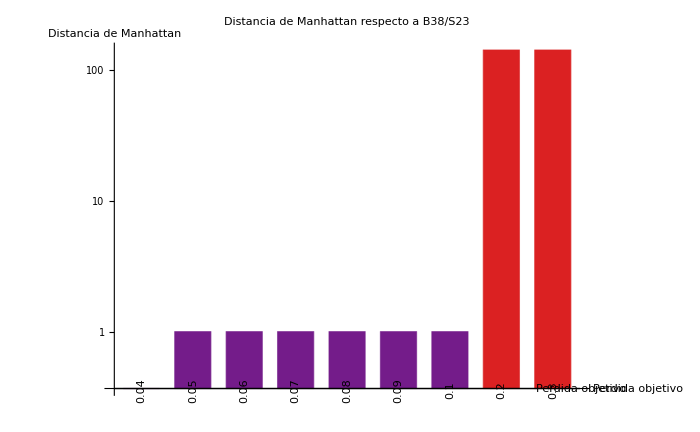

```mathematica
distancias=ManhattanDistance[basevector,#]&/@vectors;
orden=Reverse@Ordering[distancias,All,Greater];
namesSorted=names[[orden]];
distSorted=distancias[[orden]];

primerNoCero=FirstPosition[distSorted,x_/;x>0][[1]];
mask=Table[distSorted[[i]]>0||i==primerNoCero-1,{i,Length[distSorted]}];

namesFiltered=Pick[namesSorted,mask];
distFiltered=Pick[distSorted,mask];

(*Colorear según el VALOR,no según la posición*)
colorFunc=ColorData["Rainbow"];
valoresEscalados=Rescale[distFiltered]; (*normaliza entre 0 y 1*)
coloresPorValor=colorFunc/@valoresEscalados;

fplot=BarChart[distFiltered,ChartStyle->coloresPorValor,ChartLabels->Placed[Rotate[#,90 Degree]&/@namesFiltered,Axis],ScalingFunctions->"Log",AxesLabel->{"Perdida objetivo","Distancia de Manhattan"},PlotLabel->"Distancia de Manhattan respecto a B38/S23",ImageSize->700,LabelStyle->Directive[FontSize->11],BarSpacing->0.42]
```

```mathematica
SetDirectory[(NotebookDirectory[]<>"../NCA/B38S23/")];
Export["./../../../../Documentation/img/experimentacion/duplicacion/gol/b38s23_loss.png",fplot];
```

## Prueba de B3S238

Antes en NCA/B3S238/test.nb

```mathematica
tuples=Tuples[{0,1},{3,3}];
n=Length[tuples];
side=Ceiling[Sqrt[n]];
padded=PadRight[tuples,{side^2,3,3}];
blocks=Partition[padded,side];
bigMatrix=ArrayFlatten[blocks];
centers=Flatten[Table[{i,j},{i,Range[2,69,3]},{j,Range[2,69,3]}],1];
ArrayPlot[bigMatrix,Mesh->{Range[0,27*3,3],Range[0,27*3,3]},MeshStyle->Directive[Gray,Thick]]
```

-Graphics-

```mathematica
SetDirectory[(NotebookDirectory[]<>"../NCA/B3S238/")];
fns=FileNames["t_*.mat","./"];
data=Import[#,"MAT"]&/@fns;
datos=AssociationMap[Import[#,"MAT"]&,fns];
```

```mathematica
base=Import["../../CA/B3S238/base.mat","MAT"];
```

```mathematica
base[[1,2]]==#&/@datos[[;;,1,2]]
```

<|./t_00001.mat→True,./t_00002.mat→True,./t_00003.mat→True,./t_00004.mat→True,./t_00005.mat→True,./t_00006.mat→True,./t_00007.mat→True,./t_00008.mat→True,./t_00009.mat→True,./t_0001.mat→True,./t_0002.mat→True,./t_0003.mat→True,./t_0004.mat→True,./t_0005.mat→True,./t_0006.mat→True,./t_0007.mat→True,./t_0008.mat→True,./t_0009.mat→True,./t_001.mat→True,./t_002.mat→True,./t_003.mat→False,./t_004.mat→False,./t_005.mat→False,./t_006.mat→False,./t_007.mat→False,./t_008.mat→False,./t_009.mat→False,./t_01.mat→False,./t_02.mat→True,./t_03.mat→False|>

```mathematica
basevector=Flatten[Part[base[[1,2]],#[[1]],#[[2]]]&/@{#}&/@centers];
```

```mathematica
vectors=Table[
Flatten[Part[i,#[[1]],#[[2]]]&/@{#}&/@centers],
{i,datos[[;;,1,2]]}
];
```

```mathematica
names=ToExpression["0."<>StringJoin[Characters[#][[6;;-5]]]]&/@Keys[datos];
```

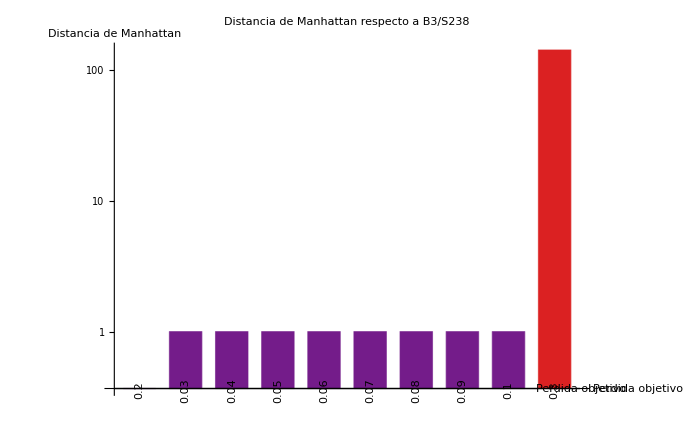

```mathematica
distancias=ManhattanDistance[basevector,#]&/@vectors;
orden=Reverse@Ordering[distancias,All,Greater];
namesSorted=names[[orden]];
distSorted=distancias[[orden]];

primerNoCero=FirstPosition[distSorted,x_/;x>0][[1]];
mask=Table[distSorted[[i]]>0||i==primerNoCero-1,{i,Length[distSorted]}];

namesFiltered=Pick[namesSorted,mask];
distFiltered=Pick[distSorted,mask];

(*Colorear según el VALOR,no según la posición*)
colorFunc=ColorData["Rainbow"];
valoresEscalados=Rescale[distFiltered]; (*normaliza entre 0 y 1*)
coloresPorValor=colorFunc/@valoresEscalados;

fplot=BarChart[distFiltered,ChartStyle->coloresPorValor,ChartLabels->Placed[Rotate[#,90 Degree]&/@namesFiltered,Axis],ScalingFunctions->"Log",AxesLabel->{"Perdida objetivo","Distancia de Manhattan"},PlotLabel->"Distancia de Manhattan respecto a B3/S238",ImageSize->700,LabelStyle->Directive[FontSize->11],BarSpacing->0.42]
```

```mathematica
life=Import["../../CA/B3S23/base.mat","MAT"];
lifevector=Flatten[Part[life[[1,2]],#[[1]],#[[2]]]&/@{#}&/@centers];
```

```mathematica
datos["./t_01.mat"][[1,2]]==life[[1,2]]
```

True

```mathematica
Keys[datos]
```

{./t_00001.mat,./t_00002.mat,./t_00003.mat,./t_00004.mat,./t_00005.mat,./t_00006.mat,./t_00007.mat,./t_00008.mat,./t_00009.mat,./t_0001.mat,./t_0002.mat,./t_0003.mat,./t_0004.mat,./t_0005.mat,./t_0006.mat,./t_0007.mat,./t_0008.mat,./t_0009.mat,./t_001.mat,./t_002.mat,./t_003.mat,./t_004.mat,./t_005.mat,./t_006.mat,./t_007.mat,./t_008.mat,./t_009.mat,./t_01.mat,./t_02.mat,./t_03.mat}

```mathematica
ArrayPlot[vectors,Mesh->True]
```

-Graphics-

```mathematica
ArrayPlot[{basevector[[-100;;-50]],vectors[[-3,-100;;-50]],lifevector[[-100;;-50]]},FrameTicks->{{{{1,"vectors[[-3]]"},{2,"lifevector"}},None},(*{left,right}*){None,None}                                         (*{bottom,top}*)},Mesh->True]
```

-Graphics-

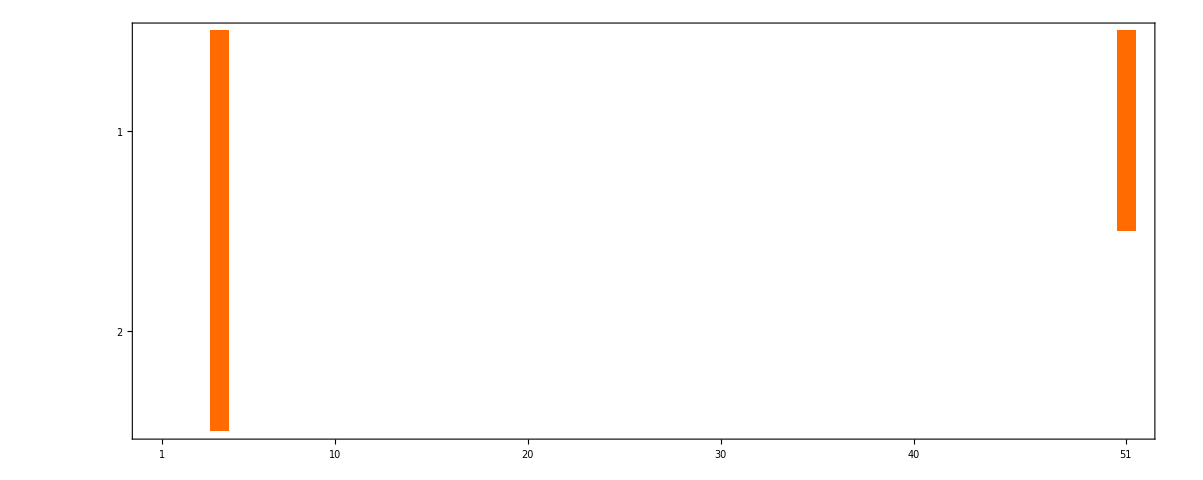

```mathematica
MatrixPlot[
{
basevector[[-68;;-18]],
lifevector[[-68;;-18]]
},Mesh->Automatic
]
```

```mathematica
Keys[datos][[-11]]
```

./t_002.mat

```mathematica
fplotc=MatrixPlot[{
basevector[[-68;;-18]],
lifevector[[-68;;-18]],
vectors[[-2,-68;;-18]],
vectors[[-3,-68;;-18]],
vectors[[-4,-68;;-18]],
vectors[[-5,-68;;-18]],
vectors[[-6,-68;;-18]],
vectors[[-7,-68;;-18]],
vectors[[-8,-68;;-18]],
vectors[[-9,-68;;-18]],
vectors[[-10,-68;;-18]],
vectors[[-11,-68;;-18]]
},FrameTicks->{{{{1,"B3/S238"},{2,"B3/S23"},{3,"NCA(0.2)"},{4,"NCA(0.1)"},{5,"NCA(0.09)"},{6,"NCA(0.08)"},{7,"NCA(0.07)"},{8,"NCA(0.06)"},{9,"NCA(0.05)"},{10,"NCA(0.04)"},{11,"NCA(0.03)"},{12,"NCA(0.02)"}},None},{None,None}},PlotLabel->"Comparación de vectores",ImagePadding->{{100,10},{30,30}},ImageSize->500,Mesh->True];
```

```mathematica
SetDirectory[(NotebookDirectory[]<>"../NCA/B3S238/")];
Export["../../../../Documentation/img/experimentacion/duplicacion/gol/b3s238_vector.png",fplotc];
```

## Prueba de B38S238

Antes en NCA/B38S238/test.nb

```mathematica
tuples=Tuples[{0,1},{3,3}];
n=Length[tuples];
side=Ceiling[Sqrt[n]];
padded=PadRight[tuples,{side^2,3,3}];
blocks=Partition[padded,side];
bigMatrix=ArrayFlatten[blocks];
centers=Flatten[Table[{i,j},{i,Range[2,69,3]},{j,Range[2,69,3]}],1];
ArrayPlot[bigMatrix,Mesh->{Range[0,27*3,3],Range[0,27*3,3]},MeshStyle->Directive[Gray,Thick]]
```

-Graphics-

```mathematica
SetDirectory[(NotebookDirectory[]<>"../NCA/B38S238/")];
fns=FileNames["t_*.mat","./"];
data=Import[#,"MAT"]&/@fns;
datos=AssociationMap[Import[#,"MAT"]&,fns];
```

```mathematica
base=Import["../../CA/B38S238/base.mat","MAT"];
```

```mathematica
base[[1,2]]==#&/@datos[[;;,1,2]]
```

<|./t_00001.mat→True,./t_00002.mat→True,./t_00003.mat→True,./t_00004.mat→True,./t_00005.mat→True,./t_00006.mat→True,./t_00007.mat→True,./t_00008.mat→True,./t_00009.mat→True,./t_0001.mat→True,./t_0002.mat→True,./t_0003.mat→True,./t_0004.mat→True,./t_0005.mat→True,./t_0006.mat→True,./t_0007.mat→True,./t_0008.mat→True,./t_0009.mat→True,./t_001.mat→True,./t_002.mat→True,./t_003.mat→True,./t_004.mat→False,./t_005.mat→False,./t_006.mat→False,./t_007.mat→False,./t_008.mat→False,./t_009.mat→False,./t_01.mat→False,./t_02.mat→False,./t_03.mat→False|>

```mathematica
basevector=Flatten[Part[base[[1,2]],#[[1]],#[[2]]]&/@{#}&/@centers];
```

```mathematica
vectors=Table[
Flatten[Part[i,#[[1]],#[[2]]]&/@{#}&/@centers],
{i,datos[[;;,1,2]]}
];
```

```mathematica
names=ToExpression["0."<>StringJoin[Characters[#][[6;;-5]]]]&/@Keys[datos];
```

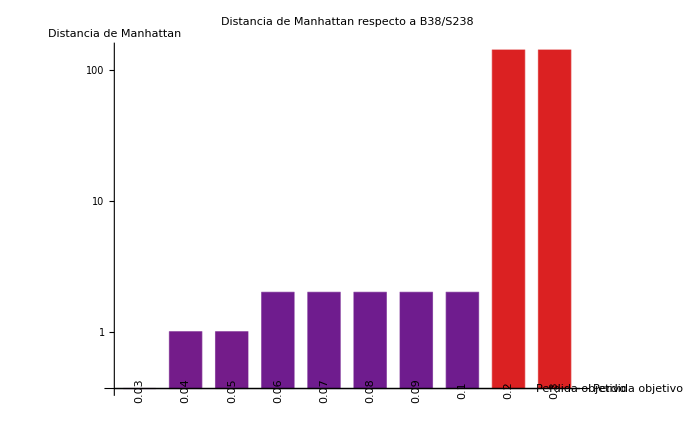

```mathematica
distancias=ManhattanDistance[basevector,#]&/@vectors;
orden=Reverse@Ordering[distancias,All,Greater];
namesSorted=names[[orden]];
distSorted=distancias[[orden]];

primerNoCero=FirstPosition[distSorted,x_/;x>0][[1]];
mask=Table[distSorted[[i]]>0||i==primerNoCero-1,{i,Length[distSorted]}];

namesFiltered=Pick[namesSorted,mask];
distFiltered=Pick[distSorted,mask];

(*Colorear según el VALOR,no según la posición*)
colorFunc=ColorData["Rainbow"];
valoresEscalados=Rescale[distFiltered]; (*normaliza entre 0 y 1*)
coloresPorValor=colorFunc/@valoresEscalados;

fplot=BarChart[distFiltered,ChartStyle->coloresPorValor,ChartLabels->Placed[Rotate[#,90 Degree]&/@namesFiltered,Axis],ScalingFunctions->"Log",AxesLabel->{"Perdida objetivo","Distancia de Manhattan"},PlotLabel->"Distancia de Manhattan respecto a B38/S238",ImageSize->700,LabelStyle->Directive[FontSize->11],BarSpacing->0.42]
```

```mathematica
SetDirectory[(NotebookDirectory[]<>"../NCA/B38S238/")];
Export["./../../../../Documentation/img/experimentacion/duplicacion/gol/b38s238_loss.png",fplot];
```

```mathematica
Keys[datos]
```

{./t_00001.mat,./t_00002.mat,./t_00003.mat,./t_00004.mat,./t_00005.mat,./t_00006.mat,./t_00007.mat,./t_00008.mat,./t_00009.mat,./t_0001.mat,./t_0002.mat,./t_0003.mat,./t_0004.mat,./t_0005.mat,./t_0006.mat,./t_0007.mat,./t_0008.mat,./t_0009.mat,./t_001.mat,./t_002.mat,./t_003.mat,./t_004.mat,./t_005.mat,./t_006.mat,./t_007.mat,./t_008.mat,./t_009.mat,./t_01.mat,./t_02.mat,./t_03.mat}

```mathematica
life=Import["../../CA/B3S23/base.mat","MAT"];
lifevector=Flatten[Part[life[[1,2]],#[[1]],#[[2]]]&/@{#}&/@centers];
life2=Import["../../CA/B3S238/base.mat","MAT"];
lifevector2=Flatten[Part[life2[[1,2]],#[[1]],#[[2]]]&/@{#}&/@centers];
```

```mathematica
fplotc=MatrixPlot[{
basevector[[-68;;-18]],
lifevector[[-68;;-18]],
lifevector2[[-68;;-18]],
vectors[[-3,-68;;-18]],
vectors[[-4,-68;;-18]],
vectors[[-5,-68;;-18]],
vectors[[-6,-68;;-18]],
vectors[[-7,-68;;-18]],
vectors[[-8,-68;;-18]],
vectors[[-9,-68;;-18]],
vectors[[-10,-68;;-18]]
},FrameTicks->{{{{1,"B38/S238"},{2,"B3/S23"},{3,"B3/S238"},{4,"NCA(0.2)"},{5,"NCA(0.1)"},{6,"NCA(0.09)"},{7,"NCA(0.08)"},{8,"NCA(0.07)"},{9,"NCA(0.06)"},{10,"NCA(0.05)"},{11,"NCA(0.04)"},{12,"NCA(0.03)"},{13,"NCA(0.02)"}},None},{None,None}},PlotLabel->"Comparación de vectores",ImagePadding->{{100,10},{30,30}},ImageSize->500,Mesh->True]
```

-Graphics-

```mathematica
SetDirectory[(NotebookDirectory[]<>"../NCA/B38S238/")];
Export["../../../../Documentation/img/experimentacion/duplicacion/gol/b38s238_vector.png",fplotc];
```

## Prueba de B3S236

Antes en NCA/B3S236/test.nb

```mathematica
tuples=Tuples[{0,1},{3,3}];
n=Length[tuples];
side=Ceiling[Sqrt[n]];
padded=PadRight[tuples,{side^2,3,3}];
blocks=Partition[padded,side];
bigMatrix=ArrayFlatten[blocks];
centers=Flatten[Table[{i,j},{i,Range[2,69,3]},{j,Range[2,69,3]}],1];
ArrayPlot[bigMatrix,Mesh->{Range[0,27*3,3],Range[0,27*3,3]},MeshStyle->Directive[Gray,Thick]]
```

-Graphics-

```mathematica
SetDirectory[(NotebookDirectory[]<>"../NCA/B3S236/")];
fns=FileNames["t_*.mat","./"];
data=Import[#,"MAT"]&/@fns;
datos=AssociationMap[Import[#,"MAT"]&,fns];
```

```mathematica
base=Import["../../CA/B3S236/base.mat","MAT"];
```

```mathematica
base[[1,2]]==#&/@datos[[;;,1,2]]
```

<|./t_00001.mat→True,./t_00002.mat→True,./t_00003.mat→True,./t_00004.mat→True,./t_00005.mat→True,./t_00006.mat→True,./t_00007.mat→True,./t_00008.mat→True,./t_00009.mat→True,./t_0001.mat→True,./t_0002.mat→True,./t_0003.mat→True,./t_0004.mat→True,./t_0005.mat→True,./t_0006.mat→True,./t_0007.mat→True,./t_0008.mat→True,./t_0009.mat→True,./t_001.mat→True,./t_002.mat→False,./t_003.mat→False,./t_004.mat→False,./t_005.mat→False,./t_006.mat→False,./t_007.mat→False,./t_008.mat→False,./t_009.mat→False,./t_01.mat→False,./t_02.mat→False,./t_03.mat→False|>

```mathematica
basevector=Flatten[Part[base[[1,2]],#[[1]],#[[2]]]&/@{#}&/@centers];
```

```mathematica
vectors=Table[
Flatten[Part[i,#[[1]],#[[2]]]&/@{#}&/@centers],
{i,datos[[;;,1,2]]}
];
```

```mathematica
names=ToExpression["0."<>StringJoin[Characters[#][[6;;-5]]]]&/@Keys[datos];
```

```mathematica
distancias=ManhattanDistance[basevector,#]&/@vectors;
orden=Reverse@Ordering[distancias,All,Greater];
namesSorted=names[[orden]];
distSorted=distancias[[orden]];

primerNoCero=FirstPosition[distSorted,x_/;x>0][[1]];
mask=Table[distSorted[[i]]>0||i==primerNoCero-1,{i,Length[distSorted]}];

namesFiltered=Pick[namesSorted,mask];
distFiltered=Pick[distSorted,mask];

(*Colorear según el VALOR,no según la posición*)
colorFunc=ColorData["Rainbow"];
valoresEscalados=Rescale[distFiltered]; (*normaliza entre 0 y 1*)
coloresPorValor=colorFunc/@valoresEscalados;

fplot=BarChart[distFiltered,ChartStyle->coloresPorValor,ChartLabels->Placed[Rotate[#,90 Degree]&/@namesFiltered,Axis],ScalingFunctions->"Log",AxesLabel->{"Perdida objetivo","Distancia de Manhattan"},PlotLabel->"Distancia de Manhattan respecto a B3/S236",ImageSize->700,LabelStyle->Directive[FontSize->11],BarSpacing->0.42]
```

-Graphics-

```mathematica
SetDirectory[(NotebookDirectory[]<>"../NCA/B3S236/")];
Export["./../../../../Documentation/img/experimentacion/duplicacion/gol/b3s236_loss.png",fplot];
```

```mathematica
Keys[datos]
```

{./t_00001.mat,./t_00002.mat,./t_00003.mat,./t_00004.mat,./t_00005.mat,./t_00006.mat,./t_00007.mat,./t_00008.mat,./t_00009.mat,./t_0001.mat,./t_0002.mat,./t_0003.mat,./t_0004.mat,./t_0005.mat,./t_0006.mat,./t_0007.mat,./t_0008.mat,./t_0009.mat,./t_001.mat,./t_002.mat,./t_003.mat,./t_004.mat,./t_005.mat,./t_006.mat,./t_007.mat,./t_008.mat,./t_009.mat,./t_01.mat,./t_02.mat,./t_03.mat}

```mathematica
Grid[{{ArrayPlot[data[[1,1,2]],Mesh->{Range[0,27*3,3],Range[0,27*3,3]},MeshStyle->Directive[Gray,Thick]],
ArrayPlot[data[[-2,1,2]],Mesh->{Range[0,27*3,3],Range[0,27*3,3]},MeshStyle->Directive[Gray,Thick]],
ArrayPlot[data[[-3,1,2]],Mesh->{Range[0,27*3,3],Range[0,27*3,3]},MeshStyle->Directive[Gray,Thick]]}}]
```

-Graphics-

```mathematica
ArrayPlot[vectors]
```

-Graphics-

```mathematica
ArrayPlot[vectors[[-3;;]],Mesh->True]
ArrayPlot[{vectors[[-1]]},Mesh->True]
ArrayPlot[{vectors[[-2]]},Mesh->True]
ArrayPlot[{vectors[[-3]]},Mesh->True]
```

-Graphics-

-Graphics-

-Graphics-

-Graphics-

```mathematica
life=Import["../../CA/B3S23/base.mat","MAT"];
lifevector=Flatten[Part[life[[1,2]],#[[1]],#[[2]]]&/@{#}&/@centers];
life2=Import["../../CA/B3S238/base.mat","MAT"];
lifevector2=Flatten[Part[life2[[1,2]],#[[1]],#[[2]]]&/@{#}&/@centers];
```

```mathematica
fplotc=MatrixPlot[{
basevector[[-68;;-18]],
lifevector[[-68;;-18]],
vectors[[-2,-68;;-18]],
vectors[[-3,-68;;-18]],
vectors[[-4,-68;;-18]],
vectors[[-5,-68;;-18]],
vectors[[-6,-68;;-18]],
vectors[[-7,-68;;-18]],
vectors[[-8,-68;;-18]],
vectors[[-9,-68;;-18]],
vectors[[-10,-68;;-18]]
},FrameTicks->{{{{1,"B38/S238"},{2,"B3/S23"},{4,"NCA(0.2)"},{5,"NCA(0.1)"},{6,"NCA(0.09)"},{7,"NCA(0.08)"},{8,"NCA(0.07)"},{9,"NCA(0.06)"},{10,"NCA(0.05)"},{11,"NCA(0.04)"},{12,"NCA(0.03)"},{13,"NCA(0.02)"}},None},{None,None}},PlotLabel->"Comparación de vectores",ImagePadding->{{100,10},{30,30}},ImageSize->500,Mesh->True]
```

-Graphics-

```mathematica
SetDirectory[(NotebookDirectory[]<>"../NCA/B3S236/")];
Export["../../../../Documentation/img/experimentacion/duplicacion/gol/b38s238_vector.png",fplotc];
```

```mathematica
diff=Flatten[Position[Abs[basevector-vectors[[-2]]],1]]
```

{128,192,224,248,252,254,255,320,352,376,380,382,383,384,416,440,444,446,447,472,476,478,479,480,500,502,503,504,506,507,509,511}

```mathematica
diftuples=tuples[[diff]]
dif2=Transpose[{basevector[[diff]],vectors[[-2,diff]]}];


Export["../../../../Documentation/img/experimentacion/duplicacion/gol/b3s236_02_10.png",Grid[Partition[
ArrayPlot[#,Mesh->True,ImageSize->40]&/@diftuples[[Flatten[Position[dif2,{1,0}]]]],UpTo[6]
],Spacings->{0, 0}]]
Export["../../../../Documentation/img/experimentacion/duplicacion/gol/b3s236_02_01.png",
Grid[{ArrayPlot[#,Mesh->True,ImageSize->40]&/@diftuples[[Flatten[Position[dif2,{0,1}]]]]},Spacings->{0, 0}]]
```

{{{0,0,1},{1,1,1},{1,1,1}},{{0,1,0},{1,1,1},{1,1,1}},{{0,1,1},{0,1,1},{1,1,1}},{{0,1,1},{1,1,0},{1,1,1}},{{0,1,1},{1,1,1},{0,1,1}},{{0,1,1},{1,1,1},{1,0,1}},{{0,1,1},{1,1,1},{1,1,0}},{{1,0,0},{1,1,1},{1,1,1}},{{1,0,1},{0,1,1},{1,1,1}},{{1,0,1},{1,1,0},{1,1,1}},{{1,0,1},{1,1,1},{0,1,1}},{{1,0,1},{1,1,1},{1,0,1}},{{1,0,1},{1,1,1},{1,1,0}},{{1,0,1},{1,1,1},{1,1,1}},{{1,1,0},{0,1,1},{1,1,1}},{{1,1,0},{1,1,0},{1,1,1}},{{1,1,0},{1,1,1},{0,1,1}},{{1,1,0},{1,1,1},{1,0,1}},{{1,1,0},{1,1,1},{1,1,0}},{{1,1,1},{0,1,0},{1,1,1}},{{1,1,1},{0,1,1},{0,1,1}},{{1,1,1},{0,1,1},{1,0,1}},{{1,1,1},{0,1,1},{1,1,0}},{{1,1,1},{0,1,1},{1,1,1}},{{1,1,1},{1,1,0},{0,1,1}},{{1,1,1},{1,1,0},{1,0,1}},{{1,1,1},{1,1,0},{1,1,0}},{{1,1,1},{1,1,0},{1,1,1}},{{1,1,1},{1,1,1},{0,0,1}},{{1,1,1},{1,1,1},{0,1,0}},{{1,1,1},{1,1,1},{1,0,0}},{{1,1,1},{1,1,1},{1,1,0}}}

../../../../Documentation/img/experimentacion/duplicacion/gol/b3s236_02_10.png

../../../../Documentation/img/experimentacion/duplicacion/gol/b3s236_02_01.png

```mathematica
diff=Flatten[Position[Abs[basevector-vectors[[-3]]],1]]
diftuples=tuples[[diff]]
dif2=Transpose[{basevector[[diff]],vectors[[-3,diff]]}]
```

{256,384,448,480,504,508,510,511,512}

{{{0,1,1},{1,1,1},{1,1,1}},{{1,0,1},{1,1,1},{1,1,1}},{{1,1,0},{1,1,1},{1,1,1}},{{1,1,1},{0,1,1},{1,1,1}},{{1,1,1},{1,1,0},{1,1,1}},{{1,1,1},{1,1,1},{0,1,1}},{{1,1,1},{1,1,1},{1,0,1}},{{1,1,1},{1,1,1},{1,1,0}},{{1,1,1},{1,1,1},{1,1,1}}}

{{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1}}

```mathematica
Export["../../../../Documentation/img/experimentacion/duplicacion/gol/b3s236_03_10.png",Grid[Partition[
ArrayPlot[#,Mesh->True,ImageSize->40]&/@diftuples[[Flatten[Position[dif2,{0,1}]]]],4
],Spacings->{0, 0}]]
Export["../../../../Documentation/img/experimentacion/duplicacion/gol/b3s236_03_01.png",
Grid[{ArrayPlot[#,Mesh->True,ImageSize->40]&/@diftuples[[Flatten[Position[dif2[[-1;;-1]],{0,1}]]]]},Spacings->{0, 0}]]
```

../../../../Documentation/img/experimentacion/duplicacion/gol/b3s236_03_10.png

../../../../Documentation/img/experimentacion/duplicacion/gol/b3s236_03_01.png

```mathematica
Grid[Partition[
ArrayPlot[#,Mesh->True,ImageSize->40]&/@diftuples[[Flatten[Position[dif2,{1,0}]]]],UpTo[6]
],Spacings->{0, 0}]
```

## Análisis inicial

Antes en notebooks/analysis.nb

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
evo1=Import["./Evolutions/gol_1000s.mat"][[1]];
evo2=Import["./Evolutions/gol_nca_2n.mat"][[1]];
```

```mathematica
diferences=Total[Unitize[#1-#2],2]&@@@Transpose[{evo1,evo2}];
```

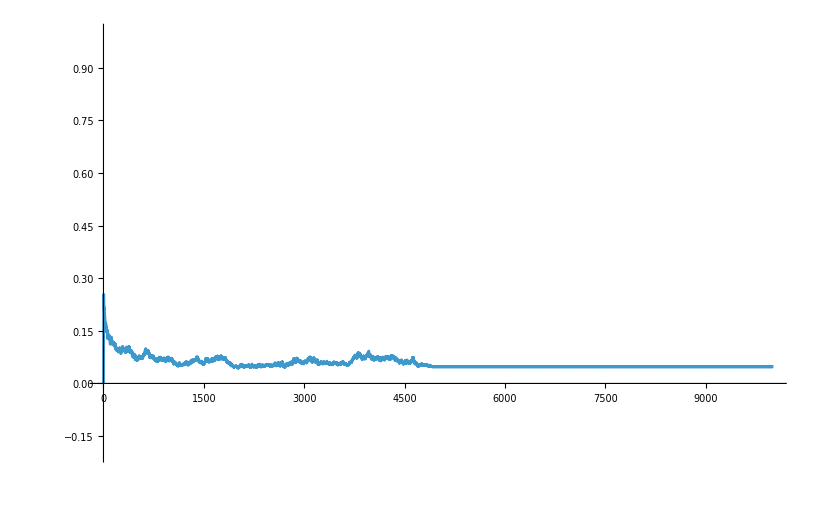

```mathematica
ListLinePlot[diferences/(100*100),PlotRange->{All,{-0.2,1}}]
```

```mathematica
Exit[]
```

```mathematica
evo1=Import["./Evolutions/gol_1000s.mat"][[1]];
evo2=CellularAutomaton["GameOfLife",evo1[[1]],1000];
```

```mathematica
plot1=ArrayPlot[evo1[[-1]]];
plot2=ArrayPlot[evo2[[-1]]];
plot3=ListPlot[Map[Total[#,2]&,Abs[evo1-evo2]],PlotLabel->"Diferencia absoluta por paso",AxesLabel->{"Paso","Pixeles discordantes"}];
```

```mathematica
Export["prueba_life_1.png",plot1,"PNG",ImageResolution->150];
Export["prueba_life_2.png",plot2,"PNG",ImageResolution->150];
Export["prueba_life_3.png",plot3,"PNG",ImageResolution->150];
```

True